```mathematica
Get["https://raw.githubusercontent.com/srossd/SCWIGE/main/Install.m"]
```

```mathematica
Needs["SCWIGE`"]
```

## 𝒩 = 2 Interface

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[U1,{{1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[1];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
Do[SetTwoPtGlobalInvariant[rep,ConjugateIrrep[GlobalSymmetry[],rep],Which[
rep[[1,1]]==2,
SparseArray[{{0,0,-1},{0,1,0},{-1,0,0}}],
rep[[1,1]]==1,
SparseArray[LeviCivitaTensor[2]],
rep[[1,1]]==0,
SparseArray[{{1}}]
]],{rep,GlobalRep/@Multiplet[1]}]
Do[
If[child1+child2===0,SetTwoPtDefectGlobalInvariant[{child1,parent1},{child2,parent2},SparseArray[{{Which[
parent1[[1,1]]==1,
If[child1==1,-1,1],
parent1[[1,1]]==2,
If[child1==0,1,-1],
True,
1
]}}]]],
{parent1,DeleteDuplicates[GlobalRep/@Multiplet[1]]},
{parent2,DeleteDuplicates[GlobalRep/@Multiplet[1]]},
{child1,SCWIGE`Private`branchingRules[][parent1]},
{child2,SCWIGE`Private`branchingRules[][parent2]}]
```

```mathematica
my3J[{u1_,p1_},{u2_,p2_},{u3_,p3_}]:=(If[u1+u2+u3!=0,0,If[p3[[1,1]]==1&&u3==1,-1,1]If[p3[[1,1]]==2&&u3==0,1,-1]ClebschGordan[{p1[[1,1]]/2,u1/2},{p2[[1,1]]/2,u2/2},{p3[[1,1]]/2,-u3/2}]]);
```

```mathematica
defectThreePtsNeeded={{{2,{{2},0}},{-1,{{1},1}},{-1,{{1},-1}}},{{0,{{2},0}},{-1,{{1},1}},{1,{{1},-1}}},{{0,{{2},0}},{1,{{1},1}},{-1,{{1},-1}}},{{-2,{{2},0}},{1,{{1},1}},{1,{{1},-1}}},{{0,{{0},2}},{1,{{1},-1}},{-1,{{1},-1}}},{{0,{{0},2}},{-1,{{1},-1}},{1,{{1},-1}}},{{0,{{0},-2}},{1,{{1},1}},{-1,{{1},1}}},{{0,{{0},-2}},{-1,{{1},1}},{1,{{1},1}}},{{0,{{0},0}},{1,{{1},1}},{-1,{{1},-1}}},{{0,{{0},0}},{-1,{{1},1}},{1,{{1},-1}}}};
fullThreePtsNeeded=DeleteDuplicates[defectThreePtsNeeded[[;;,;;,2]]];
```

```mathematica
Do[
SetThreePtDefectGlobalInvariant[Sequence@@inv,SparseArray[{{{my3J@@inv}}}]],
{inv,defectThreePtsNeeded}
];
Do[
SetThreePtGlobalInvariant[Sequence@@inv,SparseArray[Table[my3J[{u1,inv[[1]]},{u2,inv[[2]]},{u3,inv[[3]]}],
{u1,-inv[[1,1,1]],inv[[1,1,1]],2},
{u2,-inv[[2,1,1]],inv[[2,1,1]],2},
{u3,-inv[[3,1,1]],inv[[3,1,1]],2}]]],
{inv,fullThreePtsNeeded}
]
```

```mathematica
Tensor[{{"C",Raised[GlobalIndex[{{2},0}]],Raised[GlobalIndex[{{1},1}]],Raised[GlobalIndex[{{1},-1}]]}}]
Components[%]//Normal
```

C^(i_(3⊗0)i_(2⊗1)i_(2⊗-1))

({0,0} | {0,-√(2/3)}
{0,1/(√3)} | {1/(√3),0}
{-√(2/3),0} | {0,0})

```mathematica
Contract[Tensor[{{"C",Raised[GlobalIndex[{{2},0}]],Raised[GlobalIndex[{{1},1}]],Raised[GlobalIndex[{{1},-1}]]},{"C",Raised[GlobalIndex[{{2},0}]],Lowered[GlobalIndex[{{1},1}]],Lowered[GlobalIndex[{{1},-1}]]}}],{{2,5},{3,6}}]
Components[%]//Normal
```

C^(i_(3⊗0)i_(2⊗1)i_(2⊗-1))(C^(j_(3⊗0)))_(i_(2⊗1)i_(2⊗-1))

(0 | 0 | -2/3
0 | 2/3 | 0
-2/3 | 0 | 0)

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
ConjugateThreePtGlobalInvariant[{{{1},1},{{2},0}},{{1},1}]
MatrixForm/@TensorTranspose[Components[%],{2,3,1}]
```

(C_(i_(2⊗1)))^(j_(2⊗1)i_(3⊗0))

{(0 | √(2/3)
0 | 0),(-1/(√3) | 0
0 | 1/(√3)),(0 | 0
-√(2/3) | 0)}

```mathematica
full=TensorProduct[Tensor[{"K"}],NormalOrder[TensorProduct[SCWIGE`Private`defectSupercharge[1,ϕ],SCWIGE`Private`defectSupercharge[1,ϕ],Tensor[{"J"}]],"Vacuum"->True]];
corr=Correlator[full,"Defect"->True];
expanded=ExpandCorrelator[corr];
Normal[DeleteCases[ExpansionComponents[expanded],0][[;;,1,;;]]]/.SUSYRules[1]//Simplify//TableForm
```

ⅇ^(ⅈ ϕ) (24 √2 g_(1,1)^K_0j_0(u)-ⅈ √3 g_(1,1)^J_0K_0'(u)) | ⅇ^(ⅈ ϕ) (-24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | 2 ⅈ √3 (ⅇ^(ⅈ ϕ) g_(1,1)^J_0K_0(u)+ⅇ^(2 ⅈ ϕ) g_(1,1)^(K_0(K̄)_0)(u)+g_(1,1)^K_0K_0(u))
ⅇ^(ⅈ ϕ) (-24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | ⅇ^(ⅈ ϕ) (-24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | -2 ⅈ √3 (g_(1,1)^K_0K_0(u)-ⅇ^(2 ⅈ ϕ) g_(1,1)^(K_0(K̄)_0)(u))
ⅇ^(ⅈ ϕ) (24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | ⅇ^(ⅈ ϕ) (24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | -2 ⅈ √3 (g_(1,1)^K_0K_0(u)-ⅇ^(2 ⅈ ϕ) g_(1,1)^(K_0(K̄)_0)(u))
-ⅇ^(ⅈ ϕ) (24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | ⅇ^(ⅈ ϕ) (24 √2 g_(1,1)^K_0j_0(u)+ⅈ √3 g_(1,1)^J_0K_0'(u)) | 2 ⅈ √3 (ⅇ^(ⅈ ϕ) g_(1,1)^J_0K_0(u)+ⅇ^(2 ⅈ ϕ) g_(1,1)^(K_0(K̄)_0)(u)+g_(1,1)^K_0K_0(u))

```mathematica
full=TensorProduct[NormalOrder[TensorProduct[SCWIGE`Private`defectSupercharge[1,ϕ],SCWIGE`Private`defectSupercharge[1,ϕ],Tensor[{"K"}]],"Vacuum"->True],Tensor[{"J"}]];
corr=Correlator[full,"Defect"->True];
expanded=ExpandCorrelator[corr];
Normal[DeleteCases[ExpansionComponents[expanded],0][[;;,1,;;]]]/.SUSYRules[1]//Simplify//TableForm
```

-1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) g_(1,1)^(J_-2J_2)'(u) | -1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) g_(1,1)^(J_-2J_2)(u) | 
√6 ⅇ^(2 ⅈ ϕ) g_(1,1)^J_0j_0(u)+1/4 ⅈ ⅇ^(ⅈ ϕ) g_(1,1)^J_0K_0'(u) | -1/2 ⅈ ⅇ^(ⅈ ϕ) (-2 g_(1,1)^J_0K_0'(u)+ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0'(u)) | 1/6 ⅇ^(ⅈ ϕ) (4 √6 u (u+1) ⅇ^(ⅈ ϕ) g_(1,1)^J_0j_0'(u)-4 ⅈ (2 u+1) g_(1,1)^J_0K_0'(u)-6 ⅈ g_(1,1)^J_0K_0(u)-3 ⅈ ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0(u))
1/4 ⅈ ⅇ^(ⅈ ϕ) g_(1,1)^J_0K_0'(u)-√6 ⅇ^(2 ⅈ ϕ) g_(1,1)^J_0j_0(u) | -1/2 ⅈ ⅇ^(ⅈ ϕ) (-2 g_(1,1)^J_0K_0'(u)+ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0'(u)) | 1/6 ⅇ^(ⅈ ϕ) (-4 √6 u (u+1) ⅇ^(ⅈ ϕ) g_(1,1)^J_0j_0'(u)-4 ⅈ (2 u+1) g_(1,1)^J_0K_0'(u)-6 ⅈ g_(1,1)^J_0K_0(u)-3 ⅈ ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0(u))
-1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) g_(1,1)^(J_-2J_2)'(u) | -1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) g_(1,1)^(J_-2J_2)(u) |

```mathematica
corr[[-3]]
```

ⅇ^(2 ⅈ ϕ) (𝒶̄)_(K,1) (𝒶̄)_(ξ,1) τ^I_I_τ^J_J_(C^I_)_J_K_(C^K_)_I_I_ϵ^(α̇β̇)ϵ^(γ̇δ̇)ϵ^γδ(σ_1)_(αα̇)(σ_1)_(βγ̇)⟨((∂∂J)_(γδ̇δβ̇))^I_J^I_⟩_𝒟

```mathematica
expanded[[-3]]
```

ⅇ^(2 ⅈ ϕ) (𝒶̄)_(K,1) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)'(U) τ^I_I_τ^J_J_(C^I_)_J_K_(C^K_)_I_I_ϵ^(α̇β̇)ϵ^(γ̇δ̇)ϵ^γδ(σ_1)_(αα̇)(σ_1)_(βγ̇)δ^I_I_(𝒮_(u{0,2};{2,1};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(γδ̇δβ̇)+ⅇ^(2 ⅈ ϕ) (𝒶̄)_(K,1) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)(U) τ^I_I_τ^J_J_(C^I_)_J_K_(C^K_)_I_I_ϵ^(α̇β̇)ϵ^(γ̇δ̇)ϵ^γδ(σ_1)_(αα̇)(σ_1)_(βγ̇)δ^I_I_(𝒮_(∂{0,2};{2,1};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(γδ̇δβ̇)

```mathematica
List@@(D[f[u[x,y],v[x,y]]gg[x,y],{x,2},{y,0}]//Expand)//TableForm
```

2 gg^(1,0)(x,y) u^(1,0)(x,y) f^(1,0)(u(x,y),v(x,y))
2 gg^(1,0)(x,y) v^(1,0)(x,y) f^(0,1)(u(x,y),v(x,y))
gg(x,y) (v^(1,0)(x,y))^2 f^(0,2)(u(x,y),v(x,y))
2 gg(x,y) u^(1,0)(x,y) v^(1,0)(x,y) f^(1,1)(u(x,y),v(x,y))
gg(x,y) (u^(1,0)(x,y))^2 f^(2,0)(u(x,y),v(x,y))
gg^(2,0)(x,y) f(u(x,y),v(x,y))
gg(x,y) u^(2,0)(x,y) f^(1,0)(u(x,y),v(x,y))
gg(x,y) v^(2,0)(x,y) f^(0,1)(u(x,y),v(x,y))

```mathematica
testbt[{SpacetimeStructure[dims_,ls_,derivs_,perm_,q_,i_],idxs___}]/;derivs=!={}:=
Module[
{bd=SpacetimeStructures[dims,ls,{},"∂",perm,q][[i]],pd=derivs/. {type_,n_Integer}:>{type,perm[[n]]},indsPerX,siPerm,dsiPerm,siPos,dsiPos,fullPerm},
indsPerX=Table[2ls[[j]]+Count[derivs[[;;,2]],i],{j,Length[dims]}];
siPerm=Flatten@{Table[Count[derivs[[;;j-1,2]],derivs[[j,2]]]+Total[indsPerX[[;;derivs[[j,2]]-1,1]]]+1,{j,Length[derivs]}],Table[Total[indsPerX[[;;k,1]]]-2ls[[k,1]]+Range[2ls[[k,1]]],{k,Length[dims]}]};
dsiPerm=Flatten@{Table[Count[derivs[[;;j-1,2]],derivs[[j,2]]]+Total[indsPerX[[;;derivs[[j,2]]-1,2]]]+1,{j,Length[derivs]}],Table[Total[indsPerX[[;;k,2]]]-2ls[[k,2]]+Range[2ls[[k,2]]],{k,Length[dims]}]};
siPos=Position[{idxs},Lowered[Spinor]][[;;,1]];
dsiPos=Position[{idxs},Lowered[DottedSpinor]][[;;,1]];
fullPerm=SCWIGE`Private`withCounts[{idxs}]/.{{Lowered[Spinor],j_}:>siPos[[siPerm[[j]]]],{Lowered[DottedSpinor],j_}:>dsiPos[[dsiPerm[[j]]]]};
TensorPermute[Fold[Switch[#2[[1]],"∂",TensorSpinorDerivative[#1,#2[[2]]],"u",TensorProduct[TensorSpinorDerivative[u[perm],#2[[2]]],#1],"v",TensorProduct[TensorSpinorDerivative[v[perm],#2[[2]]],#1]]&,bd,Reverse[pd]],
fullPerm]
];
```

```mathematica
testbt[{SpacetimeStructure[{2,3},{{1/2,1/2},{1/2,1/2}},{{"u",1},{"∂",2}},{2,1},1,1],Lowered[Spinor],Lowered[DottedSpinor],Lowered[Spinor],Lowered[DottedSpinor],Lowered[Spinor],Lowered[DottedSpinor],Lowered[Spinor],Lowered[DottedSpinor]}]
```

(σ^μ)_(αα̇)(∂^(2))_μ(U)(σ^ν)_(γγ̇)(∂^(1))_ν((𝒮_(∂{0,0};{2,1};q = 1;1)^({2,{1/2,1/2}};{3,{1/2,1/2}}))_(ββ̇δδ̇))

```mathematica
?Fold
```

```mathematica
eqs=Thread[Flatten[%29]==0];
vars=DeleteDuplicates@Cases[eqs,g[__][__],All];
Solve[eqs,vars]
```

{}

```mathematica
SCWIGE`Private`defectSupercharge[1,ϕ]
TensorProduct[%,Tensor[{"J","ξ"}]]
NormalOrder[%,"Vacuum"->True]
Correlator[%,"Defect"->True]//TableForm
ExpandCorrelator[%]//TableForm
Normal[DeleteCases[ExpansionComponents[%],0]/.SUSYRules[1]]//TableForm
(*Cases[%,Tensor[{___,d:{"δ",_[_DefectGlobalIndex],_[_DefectGlobalIndex]},___}]:>{Rest[d],Components[Tensor[{d}]][[1,1]]},All]*)
```

(Q^(i_(2⊗1)))_α+ⅇ^(ⅈ ϕ) τ^(j_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(Q̃)_(j_(2⊗1)β̇)

(Q^(i_(2⊗1)))_αJ^(i_(3⊗0))(ξ^(j_(2⊗1)))_β+ⅇ^(ⅈ ϕ) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(Q̃)_(k_(2⊗1)β̇)J^(i_(3⊗0))(ξ^(j_(2⊗1)))_β

ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(C^(i_(3⊗0)))_(k_(2⊗1)i_(2⊗-1))((ξ̄)^(i_(2⊗-1)))_(β̇)(ξ^(j_(2⊗1)))_β+(𝒶̄)_(ξ,2) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)J^(i_(3⊗0))(C^(j_(2⊗1)))_(k_(2⊗1)i_(1⊗0))(j^(i_(1⊗0)))_(ββ̇)+(𝒶̄)_(ξ,1) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)J^(i_(3⊗0))(C^(j_(2⊗1)))_(k_(2⊗1)j_(3⊗0))∂_(ββ̇) J^(j_(3⊗0)))+𝒶_(J,1) (C_(k_(2⊗1)))^(i_(2⊗1)i_(3⊗0))(ξ^(k_(2⊗1)))_α(ξ^(j_(2⊗1)))_β+𝒶_(ξ,1) J^(i_(3⊗0))(C_(i_(1⊗2)))^(i_(2⊗1)j_(2⊗1))K^(i_(1⊗2))ϵ_αβ

ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_J_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^J_⟩_𝒟
𝒶_(J,1) C_K_^I_I_⟨(ξ^K_)_α(ξ^J_)_β⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^J_)_β⟩_𝒟+(𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
𝒶_(J,1) C_I_^I_I_⟨(ξ^I_)_α(ξ^J_)_β⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^J_)_β⟩_𝒟+(𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^I_)_β⟩_𝒟+(𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^J_⟩_𝒟)+𝒶_(J,1) C_J_^I_I_⟨(ξ^J_)_α(ξ^I_)_β⟩_𝒟+𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟
ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^I_)_β⟩_𝒟+(𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)+𝒶_(J,1) C_J_^I_I_⟨(ξ^J_)_α(ξ^I_)_β⟩_𝒟+𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟
ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^I_)_β⟩_𝒟+(𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)+𝒶_(J,1) C_J_^I_I_⟨(ξ^J_)_α(ξ^I_)_β⟩_𝒟+𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟
ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^I_)_β⟩_𝒟+(𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^J_⟩_𝒟)+𝒶_(J,1) C_J_^I_I_⟨(ξ^J_)_α(ξ^I_)_β⟩_𝒟+𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟
𝒶_(ξ,1) C_I_^I_I_ϵ_αβ⟨J^I_K^I_⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(ξ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_(j^I_)_(ββ̇)⟩_𝒟+(𝒶̄)_(ξ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
𝒶_(J,1) C_I_^I_I_⟨(ξ^I_)_α(ξ^J_)_β⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^J_)_β⟩_𝒟+(𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
𝒶_(J,1) C_K_^I_I_⟨(ξ^K_)_α(ξ^J_)_β⟩_𝒟+ⅇ^(ⅈ ϕ) ((𝒶̄)_(J,1) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((ξ̄)^I_)_(β̇)(ξ^J_)_β⟩_𝒟+(𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^I_⟩_𝒟)
ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) τ^I_I_(C^J_)_I_J_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨J^I_((∂J)_(ββ̇))^J_⟩_𝒟

0
0
-𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(U) C_I_^I_I_δ^I_J_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_βα+ⅇ^(ⅈ ϕ) ((𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)'(U) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(u{1,0};{2,1};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇)+(𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)(U) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{1,0};{2,1};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇)-(𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(U) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{0,1/2}}))_(ββ̇))
0
C_I_^I_I_ϵ_αβδ^I_I_𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{0,0}}) 𝒶_(ξ,1) g_(1,1)^J_0K_0(U)+C_J_^I_I_δ^J_I_(𝒮_(∂{0,0};{1,2};q = 1;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_αβ 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(U)+ⅇ^(ⅈ ϕ) (τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(ξ,2) g_(1,1)^J_0j_0(U)+τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(∂{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0(U)-τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{0,1/2}}))_(ββ̇) (𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(U)+τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(u{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0'(U))
0
0
C_I_^I_I_ϵ_αβδ^I_I_𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{0,0}}) 𝒶_(ξ,1) g_(1,1)^J_0K_0(U)-C_J_^I_I_δ^J_I_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_βα 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(U)+ⅇ^(ⅈ ϕ) (τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(ξ,2) g_(1,1)^J_0j_0(U)+τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(∂{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0(U)-τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{0,1/2}}))_(ββ̇) (𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(U)+τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(u{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0'(U))
0
𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(U) C_I_^I_I_δ^I_J_(𝒮_(∂{0,0};{1,2};q = 1;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_αβ+ⅇ^(ⅈ ϕ) ((𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)'(U) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(u{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇)+(𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)(U) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_I_(𝒮_(∂{0,1};{1,2};q = 1;1)^({2,{0,0}};{2,{0,0}}))_(ββ̇)-(𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(U) τ^I_I_(C^I_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)δ^I_J_(𝒮_(∂{0,0};{2,1};q = 1;1)^({5/2,{1/2,0}};{5/2,{0,1/2}}))_(ββ̇))
0
0

-ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)'(u)-2 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)-2 ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(u)
-ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)(u)-(-u-1) 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)+u ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(u)
-4 √3 ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,2) g_(1,1)^J_0j_0(u)+ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0'(u)+2 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)+2 ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(u)
1/2 √3 𝒶_(ξ,1) g_(1,1)^J_0K_0(u)+ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0(u)+(-u-1) 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)-u ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(u)
4 √3 ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,2) g_(1,1)^J_0j_0(u)+ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0'(u)-2 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)+2 ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(u)
1/2 √3 𝒶_(ξ,1) g_(1,1)^J_0K_0(u)+ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^J_0J_0(u)-(-u-1) 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)-u ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_-1(ξ̄)_1)(u)
ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)'(u)-2 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)+2 ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(u)
ⅇ^(ⅈ ϕ) (𝒶̄)_(ξ,1) g_(1,1)^(J_-2J_2)(u)+(u+1) 𝒶_(J,1) g_(1,1)^(ξ_-1ξ_1)(u)-u ⅇ^(ⅈ ϕ) (𝒶̄)_(J,1) g_(1,1)^(ξ_1(ξ̄)_-1)(u)

```mathematica
WardEquations[{"J","ξ"},"Defect"->True]//TableForm
```

1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^(J_-2J_2)'(u)-4 √3 g_(1,1)^(ξ_-1ξ_1)(u)+4 √3 ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_-1(ξ̄)_1)(u)==0
1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^(J_-2J_2)(u)-2 √3 (-u-1) g_(1,1)^(ξ_-1ξ_1)(u)-2 √3 u ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_-1(ξ̄)_1)(u)==0
12 √2 ⅇ^(ⅈ ϕ) g_(1,1)^J_0j_0(u)-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0'(u)+4 √3 g_(1,1)^(ξ_-1ξ_1)(u)-4 √3 ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_1(ξ̄)_-1)(u)==0
-ⅈ √3 g_(1,1)^J_0K_0(u)-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0(u)+2 √3 (-u-1) g_(1,1)^(ξ_-1ξ_1)(u)+2 √3 u ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_1(ξ̄)_-1)(u)==0
-12 √2 ⅇ^(ⅈ ϕ) g_(1,1)^J_0j_0(u)-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0'(u)-4 √3 g_(1,1)^(ξ_-1ξ_1)(u)-4 √3 ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_-1(ξ̄)_1)(u)==0
-ⅈ √3 g_(1,1)^J_0K_0(u)-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^J_0J_0(u)-2 √3 (-u-1) g_(1,1)^(ξ_-1ξ_1)(u)+2 √3 u ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_-1(ξ̄)_1)(u)==0
-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^(J_-2J_2)'(u)-4 √3 g_(1,1)^(ξ_-1ξ_1)(u)-4 √3 ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_1(ξ̄)_-1)(u)==0
-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) g_(1,1)^(J_-2J_2)(u)+2 √3 (u+1) g_(1,1)^(ξ_-1ξ_1)(u)+2 √3 u ⅇ^(ⅈ ϕ) g_(1,1)^(ξ_1(ξ̄)_-1)(u)==0

```mathematica
alleqs=Join[WardEquations[{"J","ξ"},"Defect"->True],WardEquations[{"J","ξ̄"},"Defect"->True]];
vars=DeleteDuplicates@Cases[alleqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>4,All];
{b,m}=Normal[CoefficientArrays[alleqs,vars]];
(consistency=NullSpace[Transpose[m]].b//Simplify)//TableForm
scpVars=Reverse@DeleteDuplicates[Cases[consistency,Derivative[__][g[x__]][y__]:>g[x][y],All]];
```

-1/2 ⅈ √3 (u+1) (g_(1,1)^(J_-2J_2)'(u)-g_(1,1)^J_0J_0'(u))
ⅈ √3 (g_(1,1)^(J_-2J_2)'(u)-g_(1,1)^J_0J_0'(u))
1/2 ⅈ √3 (-(3 u+2) g_(1,1)^J_0J_0'(u)+2 (u+1)^2 g_(1,1)^(J_-2J_2)'(u)+(4 u+2) g_(1,1)^(J_-2J_2)(u))
-2 ⅈ √3 (-g_(1,1)^J_0J_0'(u)+(u+1) g_(1,1)^(J_-2J_2)'(u)+2 g_(1,1)^(J_-2J_2)(u))
2 ⅈ √3 (-g_(1,1)^J_0J_0'(u)+(u+1) g_(1,1)^(J_-2J_2)'(u)+2 g_(1,1)^(J_-2J_2)(u))
1/2 ⅈ √3 (-g_(1,1)^J_0J_0'(u)+(u+1) g_(1,1)^(J_-2J_2)'(u)+2 g_(1,1)^(J_-2J_2)(u))
-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) (u g_(1,1)^J_0J_0'(u)+2 g_(1,1)^(J_-2J_2)(u))
-ⅈ √3 ⅇ^(ⅈ ϕ) (g_(1,1)^(J_-2J_2)'(u)-g_(1,1)^J_0J_0'(u))
-1/2 ⅈ √3 ⅇ^(ⅈ ϕ) (-u g_(1,1)^J_0J_0'(u)+2 u (u+1) g_(1,1)^(J_-2J_2)'(u)+(4 u+2) g_(1,1)^(J_-2J_2)(u))

```mathematica
SCWIGE`Private`ConformalCheck/@SpacetimeStructures[{2,3},{{0,0},{1/2,1/2}},{},"∂",{1,2}]
Simplify@*Normal@*CanonicallyOrderedComponents/@%
```

{-(TraditionalForm`x)_1^2 η^μν(∂^(1))_ν((𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇))-(TraditionalForm`x)_2^2 η^μν(∂^(2))_ν((𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇))+2 ((TraditionalForm`x)_1)^μ((TraditionalForm`x)_1)^ν(∂^(1))_ν((𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇))+2 ((TraditionalForm`x)_2)^μ((TraditionalForm`x)_2)^ν(∂^(2))_ν((𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇))+((TraditionalForm`x)_2)^ν((M^μ)_(να̇))^(β̇)(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αβ̇)+((TraditionalForm`x)_2)^ν((M^μ)_να)^β(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(βα̇)+2 (2 ((TraditionalForm`x)_1)^μ(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇)+3 ((TraditionalForm`x)_2)^μ(𝒮_(∂{0,0};{1,2};q = 1;1)^({2,{0,0}};{3,{1/2,1/2}}))_(αα̇))}

(((2 ((x_1^1)^3 (x_2^3-ⅈ x_2^4)+(x_1^1)^2 x_2^1 (-3 x_1^3+3 ⅈ x_1^4+x_2^3-ⅈ x_2^4)+((x_1^3)^2 (x_2^3-ⅈ x_2^4)-(-2 ⅈ x_2^3 x_2^4+3 (x_2^1)^2+3 (x_2^2)^2+5 (x_2^3)^2+3 (x_2^4)^2) x_1^3+(x_1^4)^2 (x_2^3-ⅈ x_2^4)+ⅈ x_1^4 (2 ⅈ x_2^3 x_2^4+3 (x_2^1)^2+3 (x_2^2)^2+3 (x_2^3)^2+5 (x_2^4)^2)+(x_2^3-ⅈ x_2^4) (-2 x_2^2 x_1^2+(x_1^2)^2+4 ((x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2))) x_1^1-3 ((x_1^2)^2+(x_1^3)^2+(x_1^4)^2) x_2^1 (x_1^3-ⅈ x_1^4-x_2^3+ⅈ x_2^4)))/((x_1^1)^3 √((x_1^1)^2) (x_2^1)^4) | 0 | 0 | 0
(-3 (x_1^1)^4 x_2^1-2 (x_1^1)^3 (-ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))-(x_1^1)^2 x_2^1 (6 ⅈ (x_2^1+ⅈ x_2^2) x_1^2-2 ⅈ x_2^1 x_2^2-6 x_1^3 x_2^3-6 x_1^4 x_2^4+6 (x_1^2)^2+6 (x_1^3)^2+6 (x_1^4)^2-(x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2)-2 (-4 ⅈ (x_2^1)^3 x_2^2-2 (x_2^1)^2 x_1^4 x_2^4-4 ⅈ (x_2^2)^3 x_2^1-4 ⅈ (x_2^3)^2 x_2^2 x_2^1-4 ⅈ (x_2^4)^2 x_2^2 x_2^1-ⅈ (x_1^4)^2 x_2^2 x_2^1+2 ⅈ x_1^4 x_2^2 x_2^4 x_2^1-4 (x_2^4)^3 x_1^4-4 (x_2^2)^2 x_1^4 x_2^4-4 (x_2^3)^2 x_1^4 x_2^4+(x_1^2)^2 (-ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))+(x_1^3)^2 (-ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))-2 x_1^3 x_2^3 (-ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))+ⅈ x_1^2 (2 ⅈ (x_2^1)^2 x_2^2+(5 (x_2^2)^2+3 ((x_2^3)^2+(x_2^4)^2)) x_2^1+4 ⅈ ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2) x_2^2+3 (x_2^1)^3)-2 (x_2^1)^4+(x_1^4)^2 (x_2^1)^2+2 (x_2^2)^4+2 (x_2^3)^4+2 (x_2^4)^4+2 (x_1^4)^2 (x_2^2)^2+2 (x_1^4)^2 (x_2^3)^2+4 (x_2^2)^2 (x_2^3)^2+2 (x_1^4)^2 (x_2^4)^2+4 (x_2^2)^2 (x_2^4)^2+4 (x_2^3)^2 (x_2^4)^2) x_1^1-3 ((x_1^2)^2+(x_1^3)^2+(x_1^4)^2) x_2^1 (2 ⅈ (x_2^1+ⅈ x_2^2) x_1^2-2 ⅈ x_2^1 x_2^2-2 x_1^3 x_2^3-2 x_1^4 x_2^4+(x_1^2)^2+(x_1^3)^2+(x_1^4)^2-(x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2))/((x_1^1)^3 √((x_1^1)^2) (x_2^1)^5) | 0 | 0 | 0) | ((-3 (x_1^1)^4 x_2^1-2 (x_1^1)^3 (ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))-(x_1^1)^2 x_2^1 ((-6 x_2^2-6 ⅈ x_2^1) x_1^2+2 ⅈ x_2^1 x_2^2-6 x_1^3 x_2^3-6 x_1^4 x_2^4+6 (x_1^2)^2+6 (x_1^3)^2+6 (x_1^4)^2-(x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2)-2 (4 ⅈ (x_2^1)^3 x_2^2-2 (x_2^1)^2 x_1^4 x_2^4+4 ⅈ (x_2^2)^3 x_2^1+4 ⅈ (x_2^3)^2 x_2^2 x_2^1+4 ⅈ (x_2^4)^2 x_2^2 x_2^1+ⅈ (x_1^4)^2 x_2^2 x_2^1-2 ⅈ x_1^4 x_2^2 x_2^4 x_2^1-4 (x_2^4)^3 x_1^4-4 (x_2^2)^2 x_1^4 x_2^4-4 (x_2^3)^2 x_1^4 x_2^4+(x_1^2)^2 (ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))+(x_1^3)^2 (ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))-2 x_1^3 x_2^3 (ⅈ x_2^2 x_2^1+(x_2^1)^2+2 ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2))-ⅈ x_1^2 (-2 ⅈ (x_2^1)^2 x_2^2+(5 (x_2^2)^2+3 ((x_2^3)^2+(x_2^4)^2)) x_2^1-4 ⅈ ((x_2^2)^2+(x_2^3)^2+(x_2^4)^2) x_2^2+3 (x_2^1)^3)-2 (x_2^1)^4+(x_1^4)^2 (x_2^1)^2+2 (x_2^2)^4+2 (x_2^3)^4+2 (x_2^4)^4+2 (x_1^4)^2 (x_2^2)^2+2 (x_1^4)^2 (x_2^3)^2+4 (x_2^2)^2 (x_2^3)^2+2 (x_1^4)^2 (x_2^4)^2+4 (x_2^2)^2 (x_2^4)^2+4 (x_2^3)^2 (x_2^4)^2) x_1^1-3 ((x_1^2)^2+(x_1^3)^2+(x_1^4)^2) x_2^1 ((-2 x_2^2-2 ⅈ x_2^1) x_1^2+2 ⅈ x_2^1 x_2^2-2 x_1^3 x_2^3-2 x_1^4 x_2^4+(x_1^2)^2+(x_1^3)^2+(x_1^4)^2-(x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2))/((x_1^1)^3 √((x_1^1)^2) (x_2^1)^5) | 0 | 0 | 0
-(2 ((x_1^1)^3 (x_2^3+ⅈ x_2^4)+(x_1^1)^2 x_2^1 (-3 x_1^3-3 ⅈ x_1^4+x_2^3+ⅈ x_2^4)+((x_1^3)^2 (x_2^3+ⅈ x_2^4)-(2 ⅈ x_2^3 x_2^4+3 (x_2^1)^2+3 (x_2^2)^2+5 (x_2^3)^2+3 (x_2^4)^2) x_1^3+(x_1^4)^2 (x_2^3+ⅈ x_2^4)-ⅈ x_1^4 (-2 ⅈ x_2^3 x_2^4+3 (x_2^1)^2+3 (x_2^2)^2+3 (x_2^3)^2+5 (x_2^4)^2)+(x_2^3+ⅈ x_2^4) (-2 x_2^2 x_1^2+(x_1^2)^2+4 ((x_2^1)^2+(x_2^2)^2+(x_2^3)^2+(x_2^4)^2))) x_1^1-3 ((x_1^2)^2+(x_1^3)^2+(x_1^4)^2) x_2^1 (x_1^3+ⅈ (x_1^4+ⅈ x_2^3-x_2^4))))/((x_1^1)^3 √((x_1^1)^2) (x_2^1)^4) | 0 | 0 | 0))

```mathematica
AddSolutions[Thread[scpVars->{𝒯[u],𝒯[u]}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
```

```mathematica
SolveWard[{"χ","Σ"},"Defect"->True]
SolveWard[{"χ̄","Σ̄"},"Defect"->True]
```

{g_(1,1)^Σ_0J_0(u)→(u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u))/(16 √6),g_(1,1)^Σ_0Σ_0(u)→1/8 (u (u (u+1) 𝒯''(u)+(6 u+4) 𝒯'(u))+(6 u+2) 𝒯(u))}

{g_(1,1)^((Σ̄)_0J_0)(u)→(-u (u+1) 𝒯''(u)-3 (2 u+1) 𝒯'(u)-6 𝒯(u))/(16 √6),g_(1,1)^((Σ̄)_0(Σ̄)_0)(u)→1/8 (u (u (u+1) 𝒯''(u)+(6 u+4) 𝒯'(u))+(6 u+2) 𝒯(u))}

```mathematica
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True]]
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
```

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_(1,1)^ϕ_0ϕ_0→{{u}↦𝒯(u)}
g_(1,1)^(ϕ_-2ϕ_2)→{{u}↦𝒯(u)}
g_(1,1)^ϕ_0J_0→{{u}↦0}
g_(1,1)^ϕ_0Σ_0→{{u}↦0}
g_(1,1)^(χ_-1(χ̄)_1)→{{u}↦-1/8 ⅈ ((u+1) 𝒯'(u)+2 𝒯(u))}
g_(1,1)^(χ_-1χ_1)→{{u}↦1/8 ⅈ (u 𝒯'(u)+2 𝒯(u))}
g_(1,1)^(χ_1(χ̄)_-1)→{{u}↦-1/8 ⅈ ((u+1) 𝒯'(u)+2 𝒯(u))}
g_(1,1)^((χ̄)_-1(χ̄)_1)→{{u}↦-1/8 ⅈ (u 𝒯'(u)+2 𝒯(u))}
g_(1,1)^(ϕ_0(Σ̄)_0)→{{u}↦0}
g_(1,1)^Σ_0J_0→{{u}↦(-u (u+1) 𝒯''(u)-3 (2 u+1) 𝒯'(u)-6 𝒯(u))/(16 √6)}
g_(1,1)^(Σ_0(Σ̄)_0)→{{u}↦1/8 ((u+1) (u (u+1) 𝒯''(u)+(6 u+2) 𝒯'(u))+(6 u+4) 𝒯(u))}
g_(1,1)^((Σ̄)_0J_0)→{{u}↦(u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u))/(16 √6)}

```mathematica
SpacetimeStructureExpressions[{{1/2,0},{0,1/2}}]
```

(I_^(1,2) | Cycles[{}])

```mathematica
NormalOrder[TensorProduct[SCWIGE`Private`defectSupercharge[1,0],Tensor[{"χ","Σ"}]],"Vacuum"->True]
Correlator[%,"Defect"->True]//TableForm
```

(𝒶̄)_(χ,1) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(C^(j_(2⊗1)))_(k_(2⊗1)i_(3⊗0))∂_(ββ̇) ϕ^(i_(3⊗0))Σ^(i_(1⊗2))+(𝒶̄)_(χ,2) τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(C^(j_(2⊗1)))_(k_(2⊗1)i_(1⊗0))(J^(i_(1⊗0)))_(ββ̇)Σ^(i_(1⊗2))+(𝒶̄)_(Σ,1) (-τ^(k_(2⊗1)i_(2⊗1))(σ_1)_(αα̇)ϵ^(α̇β̇)(χ^(j_(2⊗1)))_β(C^(i_(1⊗2)))_(k_(2⊗1)l_(2⊗1))∂_(γβ̇) (χ^(l_(2⊗1)))_δϵ^γδ)+𝒶_(χ,1) (C_(j_(1⊗2)))^(i_(2⊗1)j_(2⊗1))Σ^(j_(1⊗2))ϵ_αβΣ^(i_(1⊗2))

(𝒶̄)_(χ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((∂ϕ)_(ββ̇))^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_K_ϵ^(α̇β̇)ϵ^γδ(σ_1)_(αα̇)⟨(χ^J_)_β(((∂χ)_(γβ̇))^K_)_δ⟩_𝒟
(𝒶̄)_(χ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((∂ϕ)_(ββ̇))^I_Σ^I_⟩_𝒟+(𝒶̄)_(Σ,1) (-τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)ϵ^γδ(σ_1)_(αα̇)⟨(χ^I_)_β(((∂χ)_(γβ̇))^J_)_δ⟩_𝒟)+(𝒶̄)_(χ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨(J^I_)_(ββ̇)Σ^I_⟩_𝒟+𝒶_(χ,1) C_J_^I_I_ϵ_αβ⟨Σ^J_Σ^I_⟩_𝒟
(𝒶̄)_(χ,1) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((∂ϕ)_(ββ̇))^I_Σ^I_⟩_𝒟+(𝒶̄)_(Σ,1) (-τ^J_I_(C^I_)_J_J_ϵ^(α̇β̇)ϵ^γδ(σ_1)_(αα̇)⟨(χ^I_)_β(((∂χ)_(γβ̇))^J_)_δ⟩_𝒟)+(𝒶̄)_(χ,2) τ^J_I_(C^I_)_J_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨(J^I_)_(ββ̇)Σ^I_⟩_𝒟+𝒶_(χ,1) C_J_^I_I_ϵ_αβ⟨Σ^J_Σ^I_⟩_𝒟
(𝒶̄)_(χ,1) τ^I_I_(C^J_)_I_I_ϵ^(α̇β̇)(σ_1)_(αα̇)⟨((∂ϕ)_(ββ̇))^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_K_ϵ^(α̇β̇)ϵ^γδ(σ_1)_(αα̇)⟨(χ^J_)_β(((∂χ)_(γβ̇))^K_)_δ⟩_𝒟

```mathematica
NormalOrder[TensorProduct[SCWIGE`Private`defectSupercharge[1,0],Tensor[{"χ̄","Σ"}]],"Vacuum"->True]
Correlator[%,"Defect"->True]//TableForm
```

(𝒶̄)_(χ̄,1) τ^(j_(2⊗1)i_(2⊗1))(σ_1)_(αβ̇)ϵ^(β̇γ̇)(C^(i_(2⊗-1)))_(j_(2⊗1)i_(1⊗-2))(Σ̄)^(i_(1⊗-2))ϵ_(γ̇α̇)Σ^(i_(1⊗2))-(𝒶̄)_(Σ,1) τ^(j_(2⊗1)i_(2⊗1))(σ_1)_(αβ̇)ϵ^(β̇γ̇)((χ̄)^(i_(2⊗-1)))_(α̇)(C^(i_(1⊗2)))_(j_(2⊗1)k_(2⊗1))∂_(βγ̇) (χ^(k_(2⊗1)))_γϵ^βγ+𝒶_(χ̄,1) (C_(i_(3⊗0)))^(i_(2⊗1)i_(2⊗-1))∂_(αα̇) ϕ^(i_(3⊗0))Σ^(i_(1⊗2))+𝒶_(χ̄,2) (C_(i_(1⊗0)))^(i_(2⊗1)i_(2⊗-1))(J^(i_(1⊗0)))_(αα̇)Σ^(i_(1⊗2))

𝒶_(χ̄,1) C_I_^I_I_⟨((∂ϕ)_(αα̇))^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_J_ϵ^(β̇γ̇)ϵ^βγ(σ_1)_(αβ̇)⟨((χ̄)^I_)_(α̇)(((∂χ)_(βγ̇))^J_)_γ⟩_𝒟
(𝒶̄)_(χ̄,1) τ^I_I_(C^I_)_I_I_ϵ^(β̇γ̇)ϵ_(γ̇α̇)(σ_1)_(αβ̇)⟨(Σ̄)^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_J_ϵ^(β̇γ̇)ϵ^βγ(σ_1)_(αβ̇)⟨((χ̄)^I_)_(α̇)(((∂χ)_(βγ̇))^J_)_γ⟩_𝒟+𝒶_(χ̄,1) C_I_^I_I_⟨((∂ϕ)_(αα̇))^I_Σ^I_⟩_𝒟+𝒶_(χ̄,2) C_I_^I_I_⟨(J^I_)_(αα̇)Σ^I_⟩_𝒟
(𝒶̄)_(χ̄,1) τ^I_I_(C^I_)_I_I_ϵ^(β̇γ̇)ϵ_(γ̇α̇)(σ_1)_(αβ̇)⟨(Σ̄)^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_J_ϵ^(β̇γ̇)ϵ^βγ(σ_1)_(αβ̇)⟨((χ̄)^I_)_(α̇)(((∂χ)_(βγ̇))^J_)_γ⟩_𝒟+𝒶_(χ̄,1) C_I_^I_I_⟨((∂ϕ)_(αα̇))^I_Σ^I_⟩_𝒟+𝒶_(χ̄,2) C_I_^I_I_⟨(J^I_)_(αα̇)Σ^I_⟩_𝒟
𝒶_(χ̄,1) C_I_^I_I_⟨((∂ϕ)_(αα̇))^I_Σ^I_⟩_𝒟-(𝒶̄)_(Σ,1) τ^I_I_(C^I_)_I_J_ϵ^(β̇γ̇)ϵ^βγ(σ_1)_(αβ̇)⟨((χ̄)^I_)_(α̇)(((∂χ)_(βγ̇))^J_)_γ⟩_𝒟

```mathematica
Table[f[u],{f,Values[SolvedCorrelators[]][[;;,1]]}]/.𝒯->(u|->1/(16 u^2))//Simplify
```

{1/(16 u^2),1/(16 u^2),0,0,ⅈ/(64 u^3),0,ⅈ/(64 u^3),0,0,0,1/(64 u^3),0}

```mathematica
eqs=WardEquations[{"χ","J"},"Defect"->True]
vars=DeleteDuplicates@Cases[eqs/.(First/@SolvedCorrelators[]),g[__][__],All]
{b,m}=CoefficientArrays[eqs,vars]
NullSpace[Transpose[m]].b//Simplify
%/.(First/@SolvedCorrelators[])//Simplify
```

{-2 ⅈ √6 g_(1,1)^J_0J_0(u)-8 ⅈ √6 (u+1) g_(1,2)^J_0J_0(u)-(4 ⅈ α(7) g_(1,1)^Σ_0J_0(u))/(α(9))+(3 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+((u+1) α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))+(g_(1,1)^(χ_1(χ̄)_-1)'(u))/(√6)-√(2/3) g_(1,1)^(χ_1(χ̄)_-1)'(u)==0,-(4 ⅈ √6 u g_(1,1)^J_0J_0(u))/(u+1)-(2 α(2) g_(1,1)^ϕ_0J_0(u))/((u+1) α(9))+√(2/3) g_(1,1)^(χ_-1χ_1)'(u)-(√(2/3) u g_(1,1)^(χ_1(χ̄)_-1)'(u))/(u+1)==0,(4 ⅈ √6 u g_(1,1)^J_0J_0(u))/(u+1)+8 ⅈ √6 u g_(1,2)^J_0J_0(u)+(4 ⅈ α(7) g_(1,1)^Σ_0J_0(u))/(α(9))-((6 u+2) α(2) g_(1,1)^ϕ_0J_0(u))/(2 (u+1) α(9))-(u α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))-(g_(1,1)^(χ_-1χ_1)'(u))/(√6)+(√(2/3) u g_(1,1)^(χ_1(χ̄)_-1)'(u))/(u+1)==0,4 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)+(2 α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))+√(2/3) g_(1,1)^(χ_-1χ_1)(u)+√(2/3) g_(1,1)^(χ_1(χ̄)_-1)(u)+2/3 √(2/3) u g_(1,1)^(χ_1(χ̄)_-1)'(u)==0,-2 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)-(α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))-(g_(1,1)^(χ_-1χ_1)(u))/(√6)-(g_(1,1)^(χ_1(χ̄)_-1)(u))/(√6)-1/3 √(2/3) u g_(1,1)^(χ_1(χ̄)_-1)'(u)==0,2 ⅈ √6 g_(1,1)^J_0J_0(u)+8 ⅈ √6 (u+1) g_(1,2)^J_0J_0(u)+(4 ⅈ α(7) g_(1,1)^Σ_0J_0(u))/(α(9))+(3 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+((u+1) α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))-(g_(1,1)^(χ_-1(χ̄)_1)'(u))/(√6)+√(2/3) g_(1,1)^(χ_-1(χ̄)_1)'(u)==0,-(4 ⅈ √6 u g_(1,1)^J_0J_0(u))/(u+1)+(2 α(2) g_(1,1)^ϕ_0J_0(u))/((u+1) α(9))-(√(2/3) u g_(1,1)^(χ_-1(χ̄)_1)'(u))/(u+1)+√(2/3) g_(1,1)^(χ_-1χ_1)'(u)==0,(4 ⅈ √6 u g_(1,1)^J_0J_0(u))/(u+1)+8 ⅈ √6 u g_(1,2)^J_0J_0(u)+(4 ⅈ α(7) g_(1,1)^Σ_0J_0(u))/(α(9))+((6 u+2) α(2) g_(1,1)^ϕ_0J_0(u))/(2 (u+1) α(9))+(u α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))+(√(2/3) u g_(1,1)^(χ_-1(χ̄)_1)'(u))/(u+1)-(g_(1,1)^(χ_-1χ_1)'(u))/(√6)==0,4 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)-(2 α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))+√(2/3) g_(1,1)^(χ_-1(χ̄)_1)(u)+√(2/3) g_(1,1)^(χ_-1χ_1)(u)+2/3 √(2/3) u g_(1,1)^(χ_-1(χ̄)_1)'(u)==0,-2 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)+(α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))-(g_(1,1)^(χ_-1(χ̄)_1)(u))/(√6)-(g_(1,1)^(χ_-1χ_1)(u))/(√6)-1/3 √(2/3) u g_(1,1)^(χ_-1(χ̄)_1)'(u)==0}

{g_(1,1)^J_0J_0(u),g_(1,2)^J_0J_0(u)}

{SparseArray[…],SparseArray[…]}

{(2 α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))-(3 g_(1,1)^(χ_-1(χ̄)_1)(u)+3 g_(1,1)^(χ_-1χ_1)(u)+2 u g_(1,1)^(χ_-1(χ̄)_1)'(u)+u g_(1,1)^(χ_-1χ_1)'(u)+g_(1,1)^(χ_-1χ_1)'(u)-u g_(1,1)^(χ_1(χ̄)_-1)'(u))/(3 √6),(√6 α(9) (3 g_(1,1)^(χ_-1(χ̄)_1)(u)+3 g_(1,1)^(χ_-1χ_1)(u)+2 u g_(1,1)^(χ_-1(χ̄)_1)'(u)+u g_(1,1)^(χ_-1χ_1)'(u)+g_(1,1)^(χ_-1χ_1)'(u)-u g_(1,1)^(χ_1(χ̄)_-1)'(u))-12 α(2) g_(1,1)^ϕ_0J_0(u))/(9 α(9)),(12 ⅈ α(7) g_(1,1)^Σ_0J_0(u)+u (18 α(2) g_(1,1)^ϕ_0J_0(u)+6 (u+1) α(2) g_(1,1)^ϕ_0J_0'(u)+√6 α(9) (g_(1,1)^(χ_-1(χ̄)_1)'(u)-g_(1,1)^(χ_1(χ̄)_-1)'(u))))/(3 (u+1) α(9)),(12 α(2) g_(1,1)^ϕ_0J_0(u)+√6 u α(9) (g_(1,1)^(χ_1(χ̄)_-1)'(u)-g_(1,1)^(χ_-1(χ̄)_1)'(u)))/(3 (u+1) α(9)),(6 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+(2 (u+1) α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))+(g_(1,1)^(χ_-1(χ̄)_1)'(u)-g_(1,1)^(χ_1(χ̄)_-1)'(u))/(√6),-(3 g_(1,1)^(χ_-1χ_1)(u)+3 g_(1,1)^(χ_1(χ̄)_-1)(u)+u g_(1,1)^(χ_-1χ_1)'(u)+g_(1,1)^(χ_-1χ_1)'(u)+u g_(1,1)^(χ_1(χ̄)_-1)'(u))/(3 √6),1/3 √(2/3) (3 g_(1,1)^(χ_-1χ_1)(u)+3 g_(1,1)^(χ_1(χ̄)_-1)(u)+u g_(1,1)^(χ_-1χ_1)'(u)+g_(1,1)^(χ_-1χ_1)'(u)+u g_(1,1)^(χ_1(χ̄)_-1)'(u)),(4 ⅈ α(7) g_(1,1)^Σ_0J_0(u)-2 α(2) g_(1,1)^ϕ_0J_0(u))/(u α(9)+α(9))}

{(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(12 √6),-(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(6 √6),(ⅈ α(5) α(7) (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(4 √6 (α(9))^2 (u+1)),0,0,(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(12 √6),-(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(6 √6),(ⅈ α(5) α(7) (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(4 √6 (α(9))^2 (u+1))}

```mathematica
eqs=WardEquations[{"χ̄","J"},"Defect"->True]
vars=DeleteDuplicates@Cases[eqs/.(First/@SolvedCorrelators[]),g[__][__],All]
{b,m}=CoefficientArrays[eqs,vars]
NullSpace[Transpose[m]].b//Simplify
%/.(First/@SolvedCorrelators[])//Simplify
```

{-4 ⅈ √(2/3) u g_(1,2)^J_0J_0(u)+(2 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(3 α(9))-(α(2) g_(1,1)^ϕ_0J_0(u))/(2 α(9))+(g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(6 √6)-(u α(2) g_(1,1)^ϕ_0J_0'(u))/(6 α(9))==0,-4 ⅈ √6 g_(1,1)^J_0J_0(u)-16 ⅈ √(2/3) g_(1,2)^J_0J_0(u)+(8 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(3 u α(9))-√(2/3) (1+1/(3 u)) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-(√(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(3 u)-(2 α(2) g_(1,1)^ϕ_0J_0'(u))/(3 α(9))-√(2/3) g_(1,1)^(χ_1(χ̄)_-1)'(u)==0,2 ⅈ √6 g_(1,1)^J_0J_0(u)-8 ⅈ √(2/3) g_(1,2)^J_0J_0(u)-(8 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(3 u α(9))+((1+2/(3 u)) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(√6)+(√(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(3 u)-(α(2) g_(1,1)^ϕ_0J_0'(u))/(3 α(9))+(g_(1,1)^(χ_1(χ̄)_-1)'(u))/(√6)==0,4 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)+16/3 ⅈ √(2/3) u g_(1,2)^J_0J_0(u)-(8 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(9 α(9))+√(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)(u)-√(2/3) g_(1,1)^(χ_1(χ̄)_-1)(u)+2/9 √(2/3) (3 u+2) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)+1/9 √(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)+(2 u α(2) g_(1,1)^ϕ_0J_0'(u))/(9 α(9))==0,-2 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)-8/3 ⅈ √(2/3) u g_(1,2)^J_0J_0(u)+(4 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(9 α(9))-(g_(1,1)^((χ̄)_-1(χ̄)_1)(u))/(√6)+(g_(1,1)^(χ_1(χ̄)_-1)(u))/(√6)-1/9 √(2/3) (3 u+2) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-(g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(9 √6)-(u α(2) g_(1,1)^ϕ_0J_0'(u))/(9 α(9))==0,8 ⅈ √6 u g_(1,2)^J_0J_0(u)-(4 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(α(9))-(3 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+(g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/(√6)-√(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-(u α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))==0,-4 ⅈ √6 g_(1,1)^J_0J_0(u)-(2 α(2) g_(1,1)^ϕ_0J_0(u))/(u α(9))+√(2/3) (-1-1/u) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-√(2/3) g_(1,1)^(χ_-1(χ̄)_1)'(u)==0,2 ⅈ √6 g_(1,1)^J_0J_0(u)-8 ⅈ √6 (u+1) g_(1,2)^J_0J_0(u)+(4 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u))/(α(9))+((6+4/u) α(2) g_(1,1)^ϕ_0J_0(u))/(2 α(9))+(√(2/3) (u+1) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u))/u+((u+1) α(2) g_(1,1)^ϕ_0J_0'(u))/(α(9))+(g_(1,1)^(χ_-1(χ̄)_1)'(u))/(√6)==0,4 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)+√(2/3) g_(1,1)^((χ̄)_-1(χ̄)_1)(u)+(2 α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))-√(2/3) g_(1,1)^(χ_-1(χ̄)_1)(u)+2/3 √(2/3) (u+1) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)==0,-2 ⅈ √(2/3) u g_(1,1)^J_0J_0(u)-(g_(1,1)^((χ̄)_-1(χ̄)_1)(u))/(√6)-(α(2) g_(1,1)^ϕ_0J_0(u))/(3 α(9))+(g_(1,1)^(χ_-1(χ̄)_1)(u))/(√6)+1/3 √(2/3) (-u-1) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)==0}

{g_(1,2)^J_0J_0(u),g_(1,1)^J_0J_0(u)}

{SparseArray[…],SparseArray[…]}

{1/18 (-3 √6 g_(1,1)^((χ̄)_-1(χ̄)_1)(u)-(12 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+√6 (3 g_(1,1)^(χ_-1(χ̄)_1)(u)-(u+1) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)+u g_(1,1)^(χ_1(χ̄)_-1)'(u))),1/9 (3 √6 g_(1,1)^((χ̄)_-1(χ̄)_1)(u)+(12 α(2) g_(1,1)^ϕ_0J_0(u))/(α(9))+√6 (-3 g_(1,1)^(χ_-1(χ̄)_1)(u)+(u+1) g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-u g_(1,1)^(χ_1(χ̄)_-1)'(u))),(-24 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u)+36 (u+1) α(2) g_(1,1)^ϕ_0J_0(u)+12 u (u+1) α(2) g_(1,1)^ϕ_0J_0'(u)+√6 u α(9) (g_(1,1)^(χ_-1(χ̄)_1)'(u)-g_(1,1)^(χ_1(χ̄)_-1)'(u)))/(6 u α(9)),√(2/3) (g_(1,1)^(χ_1(χ̄)_-1)'(u)-g_(1,1)^(χ_-1(χ̄)_1)'(u))-(4 α(2) g_(1,1)^ϕ_0J_0(u))/(u α(9)),-(2 α(2) (3 g_(1,1)^ϕ_0J_0(u)+u g_(1,1)^ϕ_0J_0'(u)))/(α(9)),-(3 g_(1,1)^((χ̄)_-1(χ̄)_1)(u)-3 g_(1,1)^(χ_1(χ̄)_-1)(u)+u g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)+g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-u g_(1,1)^(χ_1(χ̄)_-1)'(u))/(3 √6),1/3 √(2/3) (3 g_(1,1)^((χ̄)_-1(χ̄)_1)(u)-3 g_(1,1)^(χ_1(χ̄)_-1)(u)+u g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)+g_(1,1)^((χ̄)_-1(χ̄)_1)'(u)-u g_(1,1)^(χ_1(χ̄)_-1)'(u)),(2 (α(2) g_(1,1)^ϕ_0J_0(u)-2 ⅈ α(5) g_(1,1)^((Σ̄)_0J_0)(u)))/(u α(9))}

{-(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(12 √6),(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(6 √6),(ⅈ α(5) α(7) (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(4 √6 (α(9))^2 u),0,0,-(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(12 √6),(ⅈ (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(6 √6),(ⅈ α(5) α(7) (u (u+1) 𝒯''(u)+(6 u+3) 𝒯'(u)+6 𝒯(u)))/(4 √6 (α(9))^2 u)}

## 𝒩 = 2 (4,0) Surface Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[2,{4,0}];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
Do[SetTwoPtGlobalInvariant[rep,ConjugateIrrep[GlobalSymmetry[],rep],SparseArray@IdentityMatrix[Times@@DimR[GlobalSymmetry[],rep]]],{rep,GlobalRep/@Multiplet[1]}]
SetTwoPtGlobalInvariant[{0},{0},SparseArray@IdentityMatrix[1]];
SetTwoPtGlobalInvariant[{2},{2},SparseArray@IdentityMatrix[3]]
SetTwoPtGlobalInvariant[{1},{1},LeviCivitaTensor[2]]
SetTwoPtGlobalInvariant[{1},AlternateRep[{1}],IdentityMatrix[2]]
SetTwoPtGlobalInvariant[AlternateRep[{1}],AlternateRep[{1}],LeviCivitaTensor[2]]
```

```mathematica
SetThreePtGlobalInvariant[{{2},0},{{1},1},{{1},-1},SparseArray[(PauliMatrix/@Range[3])]]
SetThreePtGlobalInvariant[{{0},-2},{{1},1},{{1},1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},2},{{1},-1},{{1},-1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},0},{{1},1},{{1},-1},SparseArray[{IdentityMatrix[2]}]]

SetThreePtGlobalInvariant[{2},{1},{1},SparseArray[(PauliMatrix[#].LeviCivitaTensor[2])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},{1},AlternateRep[{1}],SparseArray[(PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},AlternateRep[{1}],AlternateRep[{1}],SparseArray[(LeviCivitaTensor[2].PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{0},{1},{1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{0},{1},AlternateRep[{1}],SparseArray[{IdentityMatrix[2]}]]
SetThreePtGlobalInvariant[{0},AlternateRep[{1}],AlternateRep[{1}],SparseArray[{LeviCivitaTensor[2]}]]
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","J"},"Defect"->True,"QBar"->True]]
```

$Aborted

### Check N=(4,0) defect

```mathematica
mine=SolvedCorrelators[][g[Multiplet[1][[{5,6}]],1,1]][[1]][u,v]
```

(ⅈ (u^2 (-(g_(1,1)^ϕϕ)^(2,0)(u,v))+(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+(-3 u+ⅈ √(1-v^2)-2 v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)-u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+(g_(1,1)^ϕϕ)^(1,1)(u,v))+(2 √(1-v^2)+ⅈ v) (g_(1,1)^ϕϕ)^(0,1)(u,v))/(8 (√(1-v^2)-ⅈ v))

```mathematica
rules=First@Quiet@Solve[Cosh[ρ]==2u+v&&Exp[I θ]==v-I √(1-v^2),{u,v}]
```

{u→1/4 (-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)+2 cosh(ρ)),v→1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))}

```mathematica
Sinh[ρ]^-2 D[Sinh[ρ]^2 D[Exp[I θ]f[u,v]/.rules,ρ],ρ]+D[Exp[I θ]f[u,v]/.rules,{θ,2}]+Exp[I θ]f[u,v]/.rules
silviu=Simplify[%]/.{ρ->ArcCosh[2u+v],θ->-I Log[v-I √(1-v^2)]}//FullSimplify
```

(1/4 ⅇ^(ⅈ θ) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^4(ρ)+3/2 ⅇ^(ⅈ θ) cosh(ρ) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^2(ρ)) csch^2(ρ)+2 ⅈ ⅇ^(ⅈ θ) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+ⅇ^(ⅈ θ) (-1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+(ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,2)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))))

(-3 v^2+3 ⅈ √(1-v^2) v+2) f^(0,1)(u,v)+ⅈ (√(1-v^2)+ⅈ v) ((v^2-1) f^(0,2)(u,v)-(v^2-1) f^(1,1)(u,v)-3 (u+v) f^(1,0)(u,v)-u (u+v) f^(2,0)(u,v))-f^(1,0)(u,v)

```mathematica
Simplify[8mine-silviu/.g[__]->f]
```

0

## 𝒩 = 2 Line Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[3,0];
```

### Vector multiplet

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[\"φ\", TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{{0},2},2,{1,0},2]},{Operator["\!\(\*FormBox[OverscriptBox[\"φ\", \"_\"], TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-1},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{{0},-2},2,{0,1},-2]}},"Vector",False,1]
```

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,3];
```

```mathematica
DisplaySUSYVariations[]
```

1

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
Do[SetTwoPtGlobalInvariant[rep,ConjugateIrrep[GlobalSymmetry[],rep],SparseArray@IdentityMatrix[Times@@DimR[GlobalSymmetry[],rep]]],{rep,GlobalRep/@Multiplet[1]}]
SetTwoPtGlobalInvariant[{0},{0},SparseArray@IdentityMatrix[1]];
SetTwoPtGlobalInvariant[{2},{2},SparseArray@IdentityMatrix[3]]
SetTwoPtGlobalInvariant[{1},{1},LeviCivitaTensor[2]]
SetTwoPtGlobalInvariant[{1},AlternateRep[{1}],IdentityMatrix[2]]
SetTwoPtGlobalInvariant[AlternateRep[{1}],AlternateRep[{1}],LeviCivitaTensor[2]]
```

```mathematica
SetThreePtGlobalInvariant[{{2},0},{{1},1},{{1},-1},SparseArray[(PauliMatrix/@Range[3])]]
SetThreePtGlobalInvariant[{{0},-2},{{1},1},{{1},1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},2},{{1},-1},{{1},-1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},0},{{1},1},{{1},-1},SparseArray[{IdentityMatrix[2]}]]

SetThreePtGlobalInvariant[{2},{1},{1},SparseArray[(PauliMatrix[#].LeviCivitaTensor[2])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},{1},AlternateRep[{1}],SparseArray[(PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},AlternateRep[{1}],AlternateRep[{1}],SparseArray[(LeviCivitaTensor[2].PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{0},{1},{1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{0},{1},AlternateRep[{1}],SparseArray[{IdentityMatrix[2]}]]
SetThreePtGlobalInvariant[{0},AlternateRep[{1}],AlternateRep[{1}],SparseArray[{LeviCivitaTensor[2]}]]
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
ExpandCorrelator[Correlator[NormalOrder[TensorProduct[SCWIGE`Private`defectSupercharge[3,0],Tensor[{"χ","Σ"}]],"Vacuum"->True],"Defect"->True][[1]]]
RPart/@(List@@Expand[%])
```

(C^J_2)_K_2J_1ϵ^(α̇β̇)δ^K_2I_2(σ_4)_(αα̇)δ^I_1J_1(𝒮_(∂{0,0};{2,1};q = 3;1)^({3,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(χ,2) g_(1,1)^Σ_1J_1(U,V)+(C^J_2)_K_2J_1ϵ^(α̇β̇)δ^K_2I_2(σ_4)_(αα̇)δ^I_1J_1(𝒮_(∂{0,0};{2,1};q = 3;2)^({3,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(χ,2) g_(1,2)^Σ_1J_1(U,V)+(C^J_2)_K_2J_1ϵ^(α̇β̇)δ^K_2I_2(σ_4)_(αα̇)δ^I_1J_1(𝒮_(∂{0,0};{2,1};q = 3;3)^({3,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(χ,2) g_(1,3)^Σ_1J_1(U,V)+(C^J_2)_K_2J_1ϵ^(α̇β̇)δ^K_2I_2(σ_4)_(αα̇)δ^I_1J_1(𝒮_(∂{0,0};{2,1};q = 3;4)^({3,{0,0}};{3,{1/2,1/2}}))_(ββ̇) (𝒶̄)_(χ,2) g_(1,4)^Σ_1J_1(U,V)+C_J_1^I_2J_2ϵ_αβδ^J_1I_1𝒮_(∂{0,0};{1,2};q = 3;1)^({3,{0,0}};{3,{0,0}}) 𝒶_(χ,1) g_(1,1)^Σ_1Σ_1(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(∂{0,1};{1,2};q = 3;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) g_(1,1)^χ_2χ_2(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(∂{0,1};{1,2};q = 3;2)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) g_(1,2)^χ_2χ_2(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(∂{0,1};{1,2};q = 3;3)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) g_(1,3)^χ_2χ_2(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(∂{0,1};{1,2};q = 3;4)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) g_(1,4)^χ_2χ_2(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(v{0,1};{1,2};q = 3;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,1)^χ_2χ_2)^(0,1)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(v{0,1};{1,2};q = 3;2)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,2)^χ_2χ_2)^(0,1)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(v{0,1};{1,2};q = 3;3)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,3)^χ_2χ_2)^(0,1)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(v{0,1};{1,2};q = 3;4)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,4)^χ_2χ_2)^(0,1)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(u{0,1};{1,2};q = 3;1)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,1)^χ_2χ_2)^(1,0)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(u{0,1};{1,2};q = 3;2)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,2)^χ_2χ_2)^(1,0)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(u{0,1};{1,2};q = 3;3)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,3)^χ_2χ_2)^(1,0)(U,V)-(C^I_1)_K_2L_2ϵ^(α̇β̇)ϵ^γδδ^K_2I_2(σ_4)_(αα̇)δ^J_2L_2(𝒮_(u{0,1};{1,2};q = 3;4)^({5/2,{1/2,0}};{5/2,{1/2,0}}))_(βγβ̇δ) (𝒶̄)_(Σ,1) (g_(1,4)^χ_2χ_2)^(1,0)(U,V)

{(C^J_2)_K_2J_1δ^K_2I_2δ^I_1J_1,(C^J_2)_K_2J_1δ^K_2I_2δ^I_1J_1,(C^J_2)_K_2J_1δ^K_2I_2δ^I_1J_1,(C^J_2)_K_2J_1δ^K_2I_2δ^I_1J_1,C_J_1^I_2J_2δ^J_1I_1,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2,(C^I_1)_K_2L_2δ^K_2I_2δ^J_2L_2}

#### Sign testing

```mathematica
pairs={{"ϕ","χ"},{"ϕ","χ̄"},{"χ","Σ"},{"χ","Σ̄"},{"χ̄","Σ"},{"χ̄","Σ̄"}};
Clear[eqExpr];
eqExpr[pair_]:=eqExpr[pair]=ExpandCorrelator@Correlator[NormalOrder[TensorProduct[QTensor[]+Contract[TensorProduct[TwoPtGlobalInvariant[{2,1},{2,1}],σLowerSingle[4],ϵUpperDot,QTensor["QBar"->True]],{{2,7},{4,5},{6,8}}],Tensor[pair]],"Vacuum"->True],"Defect"->True];
signs[pair_]:=Module[{expr,structs},
expr=eqExpr[pair];
structs=DeleteDuplicates[{RPart[#],First@Cases[#,g[fields_,_,_]:>fields[[;;,1]],All,Heads->True]}&/@(List@@expr)];
Table[Labeled[Style[UndirectedEdge[pair,s[[2]]],If[ArrayRules[Flatten[Normal[CanonicallyOrderedComponents[s[[1]]]]]][[1,2]]>0,Black,Orange]],Style[s[[1]],Background->White]],{s,structs}]
]
```

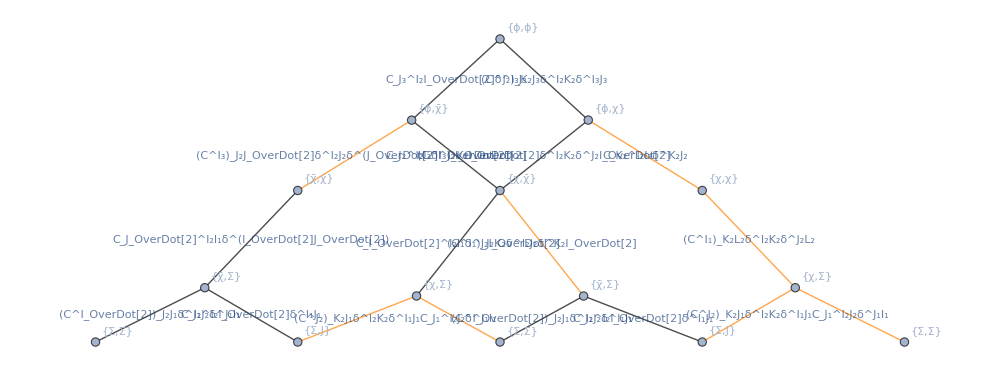

```mathematica
EdgeTaggedGraph[Join@@(signs/@pairs),VertexLabels->Automatic,VertexCoordinates->Thread[Tuples[Multiplet[2][[;;,1]],2]->({2(Last[#[[1]]]+Last[#[[2]]]),-3(ScalingDimension[#[[1]]]+ScalingDimension[#[[2]]])}&/@Tuples[Multiplet[2],2])],ImageSize->1000]
```

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True]]
AddSolutions[SolveWard[{"χ","Σ"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","Σ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","J"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","J"},"Defect"->True]]
```

$Aborted

$Aborted

```mathematica
tt=Exp[-2I φ]g[Multiplet[1][[{6,6}]],1,1][u,v]+2g[Multiplet[1][[{5,6}]],1,1][u,v]+Exp[2I φ]g[Multiplet[1][[{5,5}]],1,1][u,v]/.{{0},_}->{0}
```

2 g_(1,1)^(Σ_1(Σ̄)_1)(u,v)+ⅇ^(-2 ⅈ φ) g_(1,1)^((Σ̄)_1(Σ̄)_1)(u,v)+ⅇ^(2 ⅈ φ) g_(1,1)^Σ_1Σ_1(u,v)

```mathematica
hSolved=Collect[tt/.(First/@SolvedCorrelators[])/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->a,Derivative[__][a][__],FullSimplify]
%/.{u->U,v->V}//InputForm
```

1/4 a^(1,0)(u,v) (4 u^2-4 u (u+v) cos(2 φ)+6 u v+3 v^2-1)+1/4 a^(0,1)(u,v) ((2 u v-v^2+1) cos(2 φ)-2 u v-3 v^2+1)-1/4 (v^2-1) a^(0,2)(u,v) (u (-cos(2 φ))+u+v)+1/4 (v^2-1) a^(1,1)(u,v) (u (-cos(2 φ))+u+v)-1/4 u (u+v) a^(2,0)(u,v) (u cos(2 φ)-u-v)+1/2 a(u,v) (u-(u+v) cos(2 φ))

(a[U, V]*(U - (U + V)*Cos[2*φ]))/2 + ((1 - 2*U*V - 3*V^2 + (1 + 2*U*V - V^2)*Cos[2*φ])*Derivative[0, 1][a][U, V])/4 - 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[0, 2][a][U, V])/4 + ((-1 + 4*U^2 + 6*U*V + 3*V^2 - 4*U*(U + V)*Cos[2*φ])*Derivative[1, 0][a][U, V])/4 + 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[1, 1][a][U, V])/4 - (U*(U + V)*(-U - V + U*Cos[2*φ])*Derivative[2, 0][a][U, V])/4

```mathematica
Table[{k->SolvedCorrelators[][k][[1]][u,v]/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->({u,v}|->1/(16 u^2))},{k,Keys[SolvedCorrelators[]]}]//Simplify
```

{{g_(1,1)^(χ_2(χ̄)_OverDot[2])→ⅈ/(64 u^3)},{g_(1,2)^(χ_2(χ̄)_OverDot[2])→0},{g_(1,3)^(χ_2(χ̄)_OverDot[2])→0},{g_(1,4)^(χ_2(χ̄)_OverDot[2])→0},{g_(1,1)^χ_2χ_2→0},{g_(1,2)^χ_2χ_2→0},{g_(1,3)^χ_2χ_2→0},{g_(1,4)^χ_2χ_2→0},{g_(1,1)^((χ̄)_OverDot[2](χ̄)_OverDot[2])→0},{g_(1,2)^((χ̄)_OverDot[2](χ̄)_OverDot[2])→0},{g_(1,3)^((χ̄)_OverDot[2](χ̄)_OverDot[2])→0},{g_(1,4)^((χ̄)_OverDot[2](χ̄)_OverDot[2])→0},{g_(1,1)^Σ_1J_1→0},{g_(1,2)^Σ_1J_1→0},{g_(1,3)^Σ_1J_1→0},{g_(1,4)^Σ_1J_1→0},{g_(1,1)^(Σ_1(Σ̄)_1)→1/(64 u^3)},{g_(1,1)^Σ_1Σ_1→0},{g_(1,1)^((Σ̄)_1J_1)→0},{g_(1,2)^((Σ̄)_1J_1)→0},{g_(1,3)^((Σ̄)_1J_1)→0},{g_(1,4)^((Σ̄)_1J_1)→0},{g_(1,1)^((Σ̄)_1(Σ̄)_1)→0}}

```mathematica
Normal[SolvedCorrelators[]][[-23]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/(u(u+v))],a[u,v]|Derivative[__][a][__],FullSimplify]
```

g_(1,1)^(ΣΣ̄)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u g_(1,1)^ϕϕ(u,v)+u (g_(1,1)^ϕϕ)^(0,2)(u,v)+6 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-u (g_(1,1)^ϕϕ)^(1,1)(u,v)+v (g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,0)(u,v)-v (g_(1,1)^ϕϕ)^(1,1)(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(u-u v^2) a^(0,2)(u,v)+(1-v (2 u+v)) a^(0,1)(u,v)

```mathematica
Normal[SolvedCorrelators[]][[-22]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/u^2],a[u,v]|Derivative[__][a][__],Simplify]
```

g_(1,1)^ΣΣ→{{u,v}↦1/8 (u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-2 u v+v^2-1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 (u+v) g_(1,1)^ϕϕ(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(-2 u v-v^2+1) a^(0,1)(u,v)+(u-u v^2) a^(0,2)(u,v)

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_(1,1)^(χχ̄)→{{u,v}↦1/8 ⅈ ((g_(1,1)^ϕϕ)^(0,1)(u,v)-(g_(1,1)^ϕϕ)^(1,0)(u,v))}
g_(1,2)^(χχ̄)→{{u,v}↦1/8 ⅈ v (2 g_(1,1)^ϕϕ(u,v)+v (g_(1,1)^ϕϕ)^(0,1)(u,v)+u (g_(1,1)^ϕϕ)^(1,0)(u,v))}
g_(1,3)^(χχ̄)→{{u,v}↦0}
g_(1,4)^(χχ̄)→{{u,v}↦0}
g_(1,1)^χχ→{{u,v}↦0}
g_(1,2)^χχ→{{u,v}↦0}
g_(1,3)^χχ→{{u,v}↦1/8 (g_(1,1)^ϕϕ)^(0,1)(u,v)}
g_(1,4)^χχ→{{u,v}↦1/8 v (2 g_(1,1)^ϕϕ(u,v)+v (g_(1,1)^ϕϕ)^(0,1)(u,v)+u (g_(1,1)^ϕϕ)^(1,0)(u,v))}
g_(1,1)^(χ̄χ̄)→{{u,v}↦0}
g_(1,2)^(χ̄χ̄)→{{u,v}↦0}
g_(1,3)^(χ̄χ̄)→{{u,v}↦-1/8 (g_(1,1)^ϕϕ)^(0,1)(u,v)}
g_(1,4)^(χ̄χ̄)→{{u,v}↦-1/8 v (2 g_(1,1)^ϕϕ(u,v)+v (g_(1,1)^ϕϕ)^(0,1)(u,v)+u (g_(1,1)^ϕϕ)^(1,0)(u,v))}
g_(1,1)^ΣJ→{{u,v}↦0}
g_(1,2)^ΣJ→{{u,v}↦0}
g_(1,3)^ΣJ→{{u,v}↦-(ⅈ (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕϕ)^(1,1)(u,v)-(g_(1,1)^ϕϕ)^(0,2)(u,v))+4 u (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 g_(1,1)^ϕϕ(u,v)+(g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 (g_(1,1)^ϕϕ)^(1,0)(u,v)+u (g_(1,1)^ϕϕ)^(2,0)(u,v))))/(16 √6)}
g_(1,4)^ΣJ→{{u,v}↦(ⅈ (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+2 u (g_(1,1)^ϕϕ)^(1,0)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)-2 g_(1,1)^ϕϕ(u,v)-4 v (g_(1,1)^ϕϕ)^(0,1)(u,v)+(g_(1,1)^ϕϕ)^(0,2)(u,v)+3 v (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v)))/(8 √6)}
g_(1,1)^(ΣΣ̄)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u g_(1,1)^ϕϕ(u,v)+u (g_(1,1)^ϕϕ)^(0,2)(u,v)+6 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-u (g_(1,1)^ϕϕ)^(1,1)(u,v)+v (g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,0)(u,v)-v (g_(1,1)^ϕϕ)^(1,1)(u,v))}
g_(1,1)^ΣΣ→{{u,v}↦1/8 (u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-2 u v+v^2-1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 (u+v) g_(1,1)^ϕϕ(u,v))}
g_(1,1)^(Σ̄J)→{{u,v}↦0}
g_(1,2)^(Σ̄J)→{{u,v}↦0}
g_(1,3)^(Σ̄J)→{{u,v}↦-(ⅈ (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕϕ)^(1,1)(u,v)-(g_(1,1)^ϕϕ)^(0,2)(u,v))+4 u (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 g_(1,1)^ϕϕ(u,v)+(g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 (g_(1,1)^ϕϕ)^(1,0)(u,v)+u (g_(1,1)^ϕϕ)^(2,0)(u,v))))/(16 √6)}
g_(1,4)^(Σ̄J)→{{u,v}↦-(ⅈ (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+2 u (g_(1,1)^ϕϕ)^(1,0)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)-2 g_(1,1)^ϕϕ(u,v)-4 v (g_(1,1)^ϕϕ)^(0,1)(u,v)+(g_(1,1)^ϕϕ)^(0,2)(u,v)+3 v (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v)))/(8 √6)}
g_(1,1)^(Σ̄Σ̄)→{{u,v}↦1/8 (u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-2 u v+v^2-1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 (u+v) g_(1,1)^ϕϕ(u,v))}
g_(1,1)^JJ→{{u,v}↦(v^2 (-2 v (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 u (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 g_(1,1)^ϕϕ(u,v)+(g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+2 v^3 ((g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+v^2 (4 (g_(1,1)^ϕϕ)^(0,1)(u,v)-6 (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 u (g_(1,1)^ϕϕ)^(2,0)(u,v))+3 (g_(1,1)^ϕϕ)^(1,0)(u,v)+u (g_(1,1)^ϕϕ)^(2,0)(u,v)))/(384 u)}
g_(1,2)^JJ→{{u,v}↦-(v^2 (4 u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+16 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+6 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-4 u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+4 u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+6 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+4 u (g_(1,1)^ϕϕ)^(0,2)(u,v)+20 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 u (g_(1,1)^ϕϕ)^(1,1)(u,v)-u (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕϕ(u,v)-4 v (2 u+v) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 v (g_(1,1)^ϕϕ)^(0,2)(u,v)-3 (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 v (g_(1,1)^ϕϕ)^(1,1)(u,v)))/(384 u)}
g_(1,3)^JJ→{{u,v}↦0}
g_(1,4)^JJ→{{u,v}↦0}
g_(1,5)^JJ→{{u,v}↦(v^2 (-2 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-6 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(8 v^2-6) (g_(1,1)^ϕϕ)^(0,1)(u,v)+4 v g_(1,1)^ϕϕ(u,v)-2 v (g_(1,1)^ϕϕ)^(0,2)(u,v)-4 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 v (g_(1,1)^ϕϕ)^(1,1)(u,v)+3 (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 u (g_(1,1)^ϕϕ)^(1,1)(u,v)+u (g_(1,1)^ϕϕ)^(2,0)(u,v)))/(384 u)}
g_(1,6)^JJ→{{u,v}↦0}
g_(1,7)^JJ→{{u,v}↦0}
g_(1,8)^JJ→{{u,v}↦(v^2 (-4 u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)-8 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)-6 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)+4 u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)-4 u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+2 (8 u v+4 v^2-3) (g_(1,1)^ϕϕ)^(0,1)(u,v)-6 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)-16 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)+u (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕϕ(u,v)-2 v (g_(1,1)^ϕϕ)^(0,2)(u,v)+3 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 v (g_(1,1)^ϕϕ)^(1,1)(u,v)))/(384 u)}
g_(1,9)^JJ→{{u,v}↦0}
g_(1,10)^JJ→{{u,v}↦0}
g_(1,11)^JJ→{{u,v}↦0}
g_(1,12)^JJ→{{u,v}↦0}
g_(1,13)^JJ→{{u,v}↦(2 u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+8 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+4 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+2 u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(-4 u v-6 v^2+3) (g_(1,1)^ϕϕ)^(0,1)(u,v)+6 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+4 u g_(1,1)^ϕϕ(u,v)+2 u (g_(1,1)^ϕϕ)^(0,2)(u,v)+12 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 u (g_(1,1)^ϕϕ)^(1,1)(u,v)+2 v (g_(1,1)^ϕϕ)^(0,2)(u,v)-3 (g_(1,1)^ϕϕ)^(1,0)(u,v)-2 v (g_(1,1)^ϕϕ)^(1,1)(u,v))/(96 u)}
g_(1,14)^JJ→{{u,v}↦0}
g_(1,15)^JJ→{{u,v}↦0}
g_(1,16)^JJ→{{u,v}↦(2 u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-4 u v+2 v^2-3) (g_(1,1)^ϕϕ)^(0,1)(u,v)+4 (u+v) g_(1,1)^ϕϕ(u,v))/(96 u)}

## 𝒩 = 2

```mathematica
SetGlobalSymmetry[{SU2,U1}]
SetSignature["Euclidean"];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Flavor",True,1];
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,2];
SetMultiplet[{Operator["\!\(\*FormBox[\"M\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"Z\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Z\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[\"j1\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"j2\", TraditionalForm]\)",{{2},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"κ\", TraditionalForm]\)",{{1},1},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ\", \"_\"], TraditionalForm]\)",{{1},-1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{{0},0},4,{1,1},0]},"Stress Tensor",True,3];
```

```mathematica
IndexData[GlobalIndex[{{0},_}]]:=Index[1,"Latin",1,""&]
```

```mathematica
DisplaySUSYVariations[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

123

### Determine ⟨ϕϕϕϕ⟩

```mathematica
eqs=WardEquations[{"ϕ","ϕ","ϕ","χ̄"}]
```

{2 √2 v^3 g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-2 √2 g_(1,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+(√2 u g_(1,1)^(ϕϕχχ̄)(v/u,1/u))/v^2-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-(√2 g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(3,1)^ϕϕϕϕ(u,v))/(√2)==0,-2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3-(2 √2 g_(2,2)^(ϕϕχχ̄)(u,v) v^3)/u^3==0,(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)+(√2 g_(2,2)^(ϕϕχχ̄)(u,v))/u^2+(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,-(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)+(g_(2,1)^(ϕϕχχ̄)(u,v))/(√2)-((u-1) g_(2,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3+2 √2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) v^3==0,-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+√2 u g_(2,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u)+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2+(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)+(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,(g_(2,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3+(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3-2 √2 g_(2,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+(√2 u g_(2,1)^(ϕϕχχ̄)(v/u,1/u))/v^2+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(√2 g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0}

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,3}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v]}]
```

{g_(1,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(3)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(ϕϕχχ̄)(1/u,v/u),g_(1,2)^(ϕϕχχ̄)(v/u,1/u),g_(1,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(v/u,1/u),g_(2,2)^(ϕϕχχ̄)(u,v),g_(1,2)^ϕϕϕJ(u,v),g_(1,1)^ϕϕϕJ(u,v),g_(2,1)^(ϕϕχχ̄)(u,v),g_(1,2)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(1/u,v/u),g_(2,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(v/u,1/u),g_(2,1)^(ϕϕχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify)
```

{1/(2 √2 u)ⅈ (u (u 𝒯^(0,1)(u,v) f(1)(u,v)+((u-v) 𝒯^(0,1)(u,v)+(u-v+1) 𝒯^(1,0)(u,v)) f(2)(u,v)-(v 𝒯^(0,1)(u,v)+(u+v-1) 𝒯^(1,0)(u,v)) f(3)(u,v))+𝒯(u,v) (-2 (u-v+1) f(2)(u,v)+2 (v-1) f(3)(u,v)+u (u (f(1))^(0,1)(u,v)+(u-v) (f(2))^(0,1)(u,v)-v (f(3))^(0,1)(u,v)+u (f(2))^(1,0)(u,v)-v (f(2))^(1,0)(u,v)+(f(2))^(1,0)(u,v)-u (f(3))^(1,0)(u,v)-v (f(3))^(1,0)(u,v)+(f(3))^(1,0)(u,v)))),(ⅈ (u ((𝒯^(0,1)(u,v)+𝒯^(1,0)(u,v)) (-f(2)(u,v))+(v 𝒯^(0,1)(u,v)+(u-1) 𝒯^(1,0)(u,v)) f(3)(u,v)+((v-1) 𝒯^(0,1)(u,v)+u 𝒯^(1,0)(u,v)) f(1)(u,v))+𝒯(u,v) (2 f(2)(u,v)+2 f(3)(u,v)+u ((v-1) (f(1))^(0,1)(u,v)-(f(2))^(0,1)(u,v)+v (f(3))^(0,1)(u,v)+u (f(1))^(1,0)(u,v)-(f(2))^(1,0)(u,v)+u (f(3))^(1,0)(u,v)-(f(3))^(1,0)(u,v)))))/(√2 u v)}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform
```

{ⅈ (-2 (u-v+1) (α(2)+β(2) u+γ(2) v)+2 (v-1) (α(3)+β(3) u+γ(3) v)+u (β(2)+β(3)+β(2) u-β(3) u+γ(1) u+γ(2) (u-v)-β(2) v-β(3) v-γ(3) v))==0,ⅈ (2 (α(2)+β(2) u+γ(2) v)+2 (α(3)+β(3) u+γ(3) v)+u (-β(2)-β(3)-γ(2)+β(1) u+β(3) u+γ(1) (v-1)+γ(3) v))==0,ⅈ (u^2 (α(2)+β(2) u+γ(2) v)-u^2 (α(3)+β(3) u+γ(3) v)-u v (α(2)+β(2) u+γ(2) v)+u (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v)+u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(3)+β(3) u+γ(3) v)-u (α(2)+β(2) u+γ(2) v)-u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(2)+β(2) u+γ(2) v)-u v (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v))==0,ⅈ (-u (α(1)+β(1) u+γ(1) v)+u v (α(1)+β(1) u+γ(1) v)-u (α(2)+β(2) u+γ(2) v)+u v (α(3)+β(3) u+γ(3) v))==0}

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(2)→-α(1),α(3)→α(1),β(1)→-α(1),β(2)→α(1),β(3)→α(1),γ(1)→α(1),γ(2)→α(1),γ(3)→-α(1)}

```mathematica
Table[f[i][u,v],{i,3}]/.fform/.coeffSol/.α[1]->1
```

{-u+v+1,u+v-1,u-v+1}

### Find ,

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],(v/u)^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],u^-1 𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],u^-1 v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],u^-2 v 𝒯[u,v]];
```

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,3}]->{(1-u+v) 𝒯[u,v],(u+v-1)𝒯[u,v],(u-v+1)𝒯[u,v]}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","χ̄"}]]
```

```mathematica
Table[g[Multiplet[1][[{1,1,1,4}]],1,j][u,v],{j,2}].SpacetimeStructures[{2,2,2,3},{{0,0},{0,0},{0,0},{1/2,1/2}},{},"∂",{1,2,3,4}]/.(First/@SolvedCorrelators[])
vec=Simplify@Normal@CanonicallyOrderedComponents[1/2 Contract[TensorProduct[%,σBarLower],{{1,5},{2,4}}]];
```

((2 u v 𝒯^(0,1)(u,v)+u (u+v-1) 𝒯^(1,0)(u,v)+(u-2 v+2) 𝒯(u,v)) (𝒮_(∂{0,0,0,0};{1,2,3,4};2)^({2,{0,0}};{2,{0,0}};{2,{0,0}};{3,{1/2,1/2}}))_(αα̇))/(√3)-(u (v (u-v+1) 𝒯^(0,1)(u,v)+u (u-v-1) 𝒯^(1,0)(u,v)+(u-v+2) 𝒯(u,v)) (𝒮_(∂{0,0,0,0};{1,2,3,4};1)^({2,{0,0}};{2,{0,0}};{2,{0,0}};{3,{1/2,1/2}}))_(αα̇))/(√3)

```mathematica
sqRule={Sum[(x[i_,j]-x[j_,j])^2,{j,4}]:>XXSquared[i,j],-Sum[(x[i_,j]-x[j_,j])^2,{j,4}]:>-XXSquared[i,j]};
```

```mathematica
corr=Sum[Derivative[Sequence@@tup][𝒯][u,v](Collect[Coefficient[vec[[1]],Derivative[Sequence@@tup][𝒯][u,v]]/.sqRule/.Times[rest__,(x[i_,1]-x[j_,1])]:>Times[rest,XX[i,j]],{_XXSquared,u,v},Collect[#,_Tensor]&]/.sqRule//FullSimplify),{tup,{{0,0},{1,0},{0,1}}}]
```

(u v 𝒯^(0,1)(u,v) (-2 (TraditionalForm`x)_12^2 (TraditionalForm`x)_14^2 ((TraditionalForm`x)_(3,4))^μ+2 (TraditionalForm`x)_12^2 (TraditionalForm`x)_34^2 ((TraditionalForm`x)_(1,4))^μ+(TraditionalForm`x)_13^2 (u-v+1) ((TraditionalForm`x)_14^2 ((TraditionalForm`x)_(2,4))^μ-(TraditionalForm`x)_24^2 ((TraditionalForm`x)_(1,4))^μ)))/(√3 x_12^6 x_34^6 (TraditionalForm`x)_14^2)+(u 𝒯^(1,0)(u,v) (-((TraditionalForm`x)_12^2 (TraditionalForm`x)_14^2 (u+v-1) ((TraditionalForm`x)_(3,4))^μ)+(TraditionalForm`x)_12^2 (TraditionalForm`x)_34^2 (u+v-1) ((TraditionalForm`x)_(1,4))^μ+u (TraditionalForm`x)_13^2 (u-v-1) ((TraditionalForm`x)_14^2 ((TraditionalForm`x)_(2,4))^μ-(TraditionalForm`x)_24^2 ((TraditionalForm`x)_(1,4))^μ)))/(√3 x_12^6 x_34^6 (TraditionalForm`x)_14^2)+(𝒯(u,v) (-((TraditionalForm`x)_12^2 (TraditionalForm`x)_14^2 (u-2 v+2) ((TraditionalForm`x)_(3,4))^μ)+(TraditionalForm`x)_12^2 (TraditionalForm`x)_34^2 (u-2 v+2) ((TraditionalForm`x)_(1,4))^μ+u (TraditionalForm`x)_13^2 (u-v+2) ((TraditionalForm`x)_14^2 ((TraditionalForm`x)_(2,4))^μ-(TraditionalForm`x)_24^2 ((TraditionalForm`x)_(1,4))^μ)))/(√3 x_12^6 x_34^6 (TraditionalForm`x)_14^2)

```mathematica
CanonicallyOrderedComponents[corr]-vec//Simplify
```

{0,0,0,0}

```mathematica
corrSimp=Collect[corr/.Times[XXSquared[1,2],XXSquared[3,4]]->u XXSquared[1,3]XXSquared[2,4],_Tensor,Simplify]
```

(u v (TraditionalForm`x)_13^2 (TraditionalForm`x)_24^2 ((TraditionalForm`x)_(1,4))^μ ((u+v-1) 𝒯^(0,1)(u,v)+2 u 𝒯^(1,0)(u,v)-𝒯(u,v)))/(√3 x_12^6 x_34^6 (TraditionalForm`x)_14^2)+(u (TraditionalForm`x)_13^2 ((TraditionalForm`x)_(2,4))^μ (v (u-v+1) 𝒯^(0,1)(u,v)+u (u-v-1) 𝒯^(1,0)(u,v)+(u-v+2) 𝒯(u,v)))/(√3 x_12^6 x_34^6)-(((TraditionalForm`x)_(3,4))^μ (2 u v 𝒯^(0,1)(u,v)+u (u+v-1) 𝒯^(1,0)(u,v)+(u-2 v+2) 𝒯(u,v)))/(√3 x_12^4 x_34^6)

```mathematica
corrRescaled=Collect[Simplify[XXSquared[1,2]^2 XXSquared[3,4]^2 corrSimp]/.XXSquared[1,2]->u XXSquared[1,3] XXSquared[2,4]/XXSquared[3,4],𝒯[__]|Derivative[__][𝒯][__],Simplify]
```

(v 𝒯^(0,1)(u,v) (((TraditionalForm`x)_34^2 (u+v-1) ((TraditionalForm`x)_(1,4))^μ)/((TraditionalForm`x)_14^2)+((TraditionalForm`x)_34^2 (u-v+1) ((TraditionalForm`x)_(2,4))^μ)/((TraditionalForm`x)_24^2)-2 u ((TraditionalForm`x)_(3,4))^μ))/(√3 (TraditionalForm`x)_34^2)+(u 𝒯^(1,0)(u,v) ((TraditionalForm`x)_34^2 ((2 v ((TraditionalForm`x)_(1,4))^μ)/((TraditionalForm`x)_14^2)+((u-v-1) ((TraditionalForm`x)_(2,4))^μ)/((TraditionalForm`x)_24^2))-(u+v-1) ((TraditionalForm`x)_(3,4))^μ))/(√3 (TraditionalForm`x)_34^2)+(𝒯(u,v) ((TraditionalForm`x)_34^2 (((u-v+2) ((TraditionalForm`x)_(2,4))^μ)/((TraditionalForm`x)_24^2)-(v ((TraditionalForm`x)_(1,4))^μ)/((TraditionalForm`x)_14^2))-(u-2 v+2) ((TraditionalForm`x)_(3,4))^μ))/(√3 (TraditionalForm`x)_34^2)

```mathematica
Format[d4u,TraditionalForm]="∂_μ^(4) u";
Format[d4v,TraditionalForm]="∂_μ^(4) v";
```

```mathematica
simpleUV=Collect[corrRescaled/.{XX[3,4]->-1/2 XXSquared[3,4]/u(d4u-2u XX[2,4]/XXSquared[2,4]),XX[1,4]->-1/2 XXSquared[1,4]/v(d4v-2v XX[2,4]/XXSquared[2,4])},𝒯[__]|Derivative[__][𝒯][__],Simplify]
```

(𝒯^(0,1)(u,v) (2 ∂_μ^(4) u v-∂_μ^(4) v (u+v-1)))/(2 √3)+(𝒯^(1,0)(u,v) (∂_μ^(4) u (u+v-1)-2 ∂_μ^(4) v u))/(2 √3)+(𝒯(u,v) (∂_μ^(4) u (u-2 v+2)+∂_μ^(4) v u))/(2 √3 u)

```mathematica
uv2τθ={u->2Exp[τ](Cosh[τ]-Cos[θ]),v->Exp[2τ]};
τθ2uv=Assuming[u>0&&v>0,Simplify@Last@Solve[Equal@@@uv2τθ,{τ,θ}]]/.C[_]->0;
```

```mathematica
D[Values[uv2τθ]/.{τ->τ[y],θ->θ[y]},y]/.{τ[y]->τ,θ[y]->θ,τ'[y]->d4τ,θ'[y]->d4θ}
```

{2 ⅇ^τ (d4θ sin(θ)+d4τ sinh(τ))+2 d4τ ⅇ^τ (cosh(τ)-cos(θ)),2 d4τ ⅇ^(2 τ)}

```mathematica
Assuming[0<θ<π&&τ∈Reals,FullSimplify[simpleUV/.𝒯->Function[{u,v},Evaluate[𝒯[τ,θ]/.τθ2uv]]/.uv2τθ/.Thread[{d4u,d4v}->(D[Values[uv2τθ]/.{τ->τ[y],θ->θ[y]},y]/.{τ[y]->τ,θ[y]->θ,τ'[y]->d4τ,θ'[y]->d4θ})]]]
```

(ⅇ^τ (𝒯(τ,θ) (cosh(τ) (6 d4τ cos(θ)-2 d4θ sin(θ))+2 d4θ sin(θ) (cos(θ)+2 sinh(τ))-d4τ (cos(2 θ)+5))-2 sin(θ) (cos(θ)-cosh(τ)) (d4τ 𝒯^(0,1)(τ,θ)-d4θ 𝒯^(1,0)(τ,θ))))/(2 √3 (cos(θ)-cosh(τ)))

```mathematica
xx=Array[x,4];
one={1,0,0,0};
uvRule={u->Total[(xx-one)^2],v->Total[xx^2],d4u->2(xx-one),d4v->2xx};
```

```mathematica
(inX=FullSimplify[simpleUV/.uvRule])//TableForm
```

((2 ((x(2))^2+(x(3))^2+(x(4))^2-3 (x(1)-2) x(1)-3) 𝒯((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2))/((x(2))^2+(x(3))^2+(x(4))^2+(x(1)-2) x(1)+1)-4 ((x(2))^2+(x(3))^2+(x(4))^2) (𝒯^(0,1)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)+𝒯^(1,0)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)))/(2 √3)
(2 x(2) (x(1) 𝒯^(0,1)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)+(x(1)-1) 𝒯^(1,0)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)-(2 (x(1)-1) 𝒯((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2))/((x(2))^2+(x(3))^2+(x(4))^2+(x(1)-2) x(1)+1)))/(√3)
(2 x(3) (x(1) 𝒯^(0,1)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)+(x(1)-1) 𝒯^(1,0)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)-(2 (x(1)-1) 𝒯((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2))/((x(2))^2+(x(3))^2+(x(4))^2+(x(1)-2) x(1)+1)))/(√3)
(2 x(4) (x(1) 𝒯^(0,1)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)+(x(1)-1) 𝒯^(1,0)((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2)-(2 (x(1)-1) 𝒯((x(1)-1)^2+(x(2))^2+(x(3))^2+(x(4))^2,(x(1))^2+(x(2))^2+(x(3))^2+(x(4))^2))/((x(2))^2+(x(3))^2+(x(4))^2+(x(1)-2) x(1)+1)))/(√3)

```mathematica
inX-1/(√3)(u^2(one.Table[D[𝒯[u,v]/u^2/.uvRule,y],{y,xx}]xx-Sum[D[y 𝒯[u,v]/u^2/.uvRule,y],{y,xx}]one)+𝒯[u,v]one)/.uvRule//Simplify
```

{0,0,0,0}

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","J","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ","χ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","Σ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ","Σ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","χ","Σ̄"}]];
```

### Find

```mathematica
DeclareArbitraryFunction[𝒫];
DeclareCrossingRule[𝒫[v,u],𝒫[v,u]];
DeclareCrossingRule[𝒫[u/v,1/v],𝒫[u,v]];
DeclareCrossingRule[𝒫[1/u,v/u],𝒫[1/u,v/u]];
DeclareCrossingRule[𝒫[v/u,1/u],𝒫[v,u]];
DeclareCrossingRule[𝒫[1/v,u/v],𝒫[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[1][[1]],Multiplet[1][[1]]},1,1][u,v]->𝒫[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ","Σ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ̄","Σ"},"QBar"->True]]
```

### Find , ,

```mathematica
DeclareArbitraryFunction[𝒲];
DeclareCrossingRule[𝒲[v,u],𝒲[v,u]];
DeclareCrossingRule[𝒲[u/v,1/v],𝒲[u,v]];
DeclareCrossingRule[𝒲[1/u,v/u],𝒲[1/u,v/u]];
DeclareCrossingRule[𝒲[v/u,1/u],𝒲[v,u]];
DeclareCrossingRule[𝒲[1/v,u/v],𝒲[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[3][[1]],Multiplet[3][[1]]},1,1][u,v]->𝒲[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","Z̄"}]]
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","Z"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j1"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","j1"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j2"}]]
```

$Aborted

```mathematica
Put[SolvedCorrelators[],"n2_correlators_test.m"]
```

## 𝒩 = 4 Vector

```mathematica
SetRSymmetry[SU4]
SetMultiplet[{Operator["\!\(\*FormBox[\"X\", TraditionalForm]\)",{0,1,0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,0,0},2,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,0,0},2,{0,1},-2]},"Vector",True,1];
```

```mathematica
DisplaySUSYVariations["Solved"->False]
```

1

## 𝒩 = 4 Stress tensor

```mathematica
SetGlobalSymmetry[SU4];
SetSignature["Euclidean"];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
Get["C:/users/rossd/downloads/ThreePtStructures2.txt"];
Get["C:/users/rossd/downloads/FourPtStructures2.txt"];
```

```mathematica
SetTwoPtGlobalInvariant[6,6,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6}]]];
SetTwoPtGlobalInvariant[4,-4,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}]]];
SetTwoPtGlobalInvariant[1,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,1},{j,1,1}]]];
SetTwoPtGlobalInvariant[10,-10,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10}]]];
SetTwoPtGlobalInvariant[15,15,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15}]]];
SetTwoPtGlobalInvariant[20,-20,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
SetTwoPtGlobalInvariant[{0,2,0},{0,2,0},SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
```

```mathematica
SetThreePtGlobalInvariant[4,{0,2,0},-20,SparseArray[threeptinvt420p20b]];
SetThreePtGlobalInvariant[4,20,10,SparseArray[threeptinvt42010]];
SetThreePtGlobalInvariant[4,20,6,SparseArray[threeptinvt4206]];
SetThreePtGlobalInvariant[4,6,4,SparseArray[threeptinvt464]];
SetThreePtGlobalInvariant[4,-4,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4},{k,1,1}]]];
SetThreePtGlobalInvariant[4,-20,15,SparseArray[Conjugate[threeptinvt4b2015]]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[4,-10,4,SparseArray[threeptinvt410b4]];
SetThreePtGlobalInvariant[-4,{0,2,0},20,SparseArray[Conjugate[threeptinvt420p20b]]];
SetThreePtGlobalInvariant[-4,-20,-10,SparseArray[Conjugate[threeptinvt42010]]];
SetThreePtGlobalInvariant[-4,-20,-6,SparseArray[Conjugate[threeptinvt4206]]];
SetThreePtGlobalInvariant[-4,6,-4,SparseArray[Conjugate[threeptinvt464]]];
SetThreePtGlobalInvariant[-4,20,15,SparseArray[threeptinvt4b2015]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[-4,10,-4,SparseArray[Conjugate[threeptinvt410b4]]];
```

```mathematica
SetThreePtGlobalInvariant[{0,2,0},6,6,SparseArray[threeptinvt20p66]];
SetThreePtGlobalInvariant[15,6,6,SparseArray[threeptinvt1566]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},15,SparseArray[threeptinvt20p20p15]];
SetThreePtGlobalInvariant[{0,2,0},15,15,SparseArray[threeptinvt20p1515]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},{0,2,0},SparseArray[threeptinvt20p20p20p]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[20,-20,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[15,15,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15},{k,1,1}]]];
SetThreePtGlobalInvariant[6,6,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6},{k,1,1}]]];
SetThreePtGlobalInvariant[10,-10,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10},{k,1,1}]]];
SetThreePtGlobalInvariant[{0,2,0},20,-20,SparseArray[threeptinvt20p2020b]];
SetThreePtGlobalInvariant[{0,2,0},10,10,SparseArray[threeptinvt20p1010]];
SetThreePtGlobalInvariant[{0,2,0},-10,-10,SparseArray[Conjugate[threeptinvt20p1010]]];
SetThreePtGlobalInvariant[20,20,6,SparseArray[threeptinvt20206]];
SetThreePtGlobalInvariant[-20,-20,6,SparseArray[Conjugate[threeptinvt20206]]];
SetThreePtGlobalInvariant[20,20,10,SparseArray[threeptinvt202010]];
SetThreePtGlobalInvariant[-20,-20,-10,SparseArray[Conjugate[threeptinvt202010]]];
SetThreePtGlobalInvariant[10,-10,15,SparseArray[threeptinvt1010b15]];
SetThreePtGlobalInvariant[6,10,15,SparseArray[threeptinvt61015]];
SetThreePtGlobalInvariant[6,-10,15,SparseArray[Conjugate[threeptinvt61015]]];
```

```mathematica
SetThreePtGlobalInvariant[20,20,-10,SparseArray[threeptinvt202010b]];
SetThreePtGlobalInvariant[-20,-20,10,SparseArray[Conjugate@threeptinvt202010b]];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],v^2/u^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],v^2/u^2 𝒯[u,v]];
```

### Find

```mathematica
eqs=WardEquations[{"S","S","S","χ̄"}];
```

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_(1,1)^SSSS→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^SSSS→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^SSSS→({u,v}↦𝒯(u,v) f(3)(u,v)),g_(4,1)^SSSS→({u,v}↦𝒯(u,v) f(4)(u,v)),g_(5,1)^SSSS→({u,v}↦𝒯(u,v) f(5)(u,v)),g_(6,1)^SSSS→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(SSχχ̄)(1/u,v/u),g_(1,2)^(SSχχ̄)(u,v),g_(2,2)^(SSχχ̄)(1/u,v/u),g_(2,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(1/u,v/u),g_(2,1)^(SSχχ̄)(1/u,v/u),g_(1,1)^(SSχχ̄)(u,v),g_(2,1)^(SSχχ̄)(u,v),g_(1,2)^(SSχχ̄)(v/u,1/u),g_(2,2)^(SSχχ̄)(v/u,1/u),g_(3,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(v/u,1/u),g_(2,1)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^(SSχχ̄)(u,v),g_(3,2)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(v/u,1/u),g_(4,2)^(SSχχ̄)(u,v),g_(1,2)^SSSJ(u,v),g_(1,1)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(u,v),g_(4,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^SSSJ(u,v),g_(4,2)^(SSχχ̄)(v/u,1/u),g_(4,1)^(SSχχ̄)(v/u,1/u),g_(5,2)^(SSχχ̄)(u,v),g_(2,2)^SSSJ(u,v),g_(2,1)^SSSJ(u,v),g_(5,1)^(SSχχ̄)(u,v),g_(5,2)^(SSχχ̄)(1/u,v/u),g_(5,1)^(SSχχ̄)(1/u,v/u),g_(5,2)^(SSχχ̄)(v/u,1/u),g_(5,1)^(SSχχ̄)(v/u,1/u),g_(6,2)^(SSχχ̄)(u,v),g_(6,1)^(SSχχ̄)(u,v),g_(6,2)^(SSχχ̄)(1/u,v/u),g_(6,1)^(SSχχ̄)(1/u,v/u),g_(6,2)^(SSχχ̄)(v/u,1/u),g_(6,1)^(SSχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify);
```

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ξ[i] v^2));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform;
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(1)→0,α(2)→0,α(3)→0,α(5)→0,α(6)→0,β(1)→0,β(2)→0,β(3)→16 α(4),β(4)→-α(4),β(5)→0,β(6)→-α(4),γ(1)→16 α(4),γ(2)→0,γ(3)→0,γ(4)→-α(4),γ(5)→-α(4),γ(6)→0,δ(1)→0,δ(2)→16 α(4),δ(3)→0,δ(4)→0,δ(5)→-α(4),δ(6)→-α(4),ζ(1)→0,ζ(2)→0,ζ(3)→0,ζ(4)→0,ζ(5)→0,ζ(6)→α(4),ξ(1)→0,ξ(2)→0,ξ(3)→0,ξ(4)→0,ξ(5)→α(4),ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.α[4]->1/16//Simplify
```

{v,u v,u,1/16 (-u-v+1),1/16 v (-u+v-1),1/16 u (u-v-1)}

### Solve identities

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,6}]->(multipliers 𝒯[u,v])]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","S","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F̄","χ"}]];
```

```mathematica
AbsoluteTiming[AddSolutions[SolveWard[{"S","S","χ̄","J"}]]]
```

{153.23,Null}

```mathematica
repeats=Select[SolvedCorrelators[],Length[#]>1&];
Flatten@Table[FullSimplify[Differences@Table[ff[u,v],{ff,repeats[Keys[repeats][[i]]]}],u>0&&v>0],{i,Length[repeats]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Long

```mathematica
SetRSymmetry[SU4]
```

```mathematica
SetMultiplet[(<<"ward/long_multiplet.m"),"Long",True,1]
```

```mathematica
Simplify[#,Δ!=0&&_SUSYCoefficient != 0]&/@SCWIGE`Private`linearEquations[1,"MaxDepth"->2]
```

{Δ==(ⅈ 𝒶_(𝒪(0,0,1),1))/(2 𝒶_(𝒪(0,1,1),3)),Δ==(ⅈ (𝒶̄)_(𝒪(0,0,1),1))/(2 (𝒶̄)_(𝒪(1,0,1),3)),Δ==-(√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2)-ⅈ 𝒶_(𝒪(0,1,1),2))/(4 𝒶_(𝒪(1,1,1),3))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),2)+√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2))/(4 𝒶_(𝒪(1,1,1),3)),2 Δ+(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4))),Δ==-(√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2)-ⅈ 𝒶_(𝒪(0,1,1),1))/(4 𝒶_(𝒪(1,1,2),5))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),1)+√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2))/(4 𝒶_(𝒪(1,1,2),5)),2 Δ+(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6))),2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,Δ==(ⅈ (𝒶̄)_(𝒪(0,1,1),1))/(2 (𝒶̄)_(𝒪(2,0,2),4))+1,Δ==(ⅈ 𝒶_(𝒪(1,0,1),1))/(2 𝒶_(𝒪(0,2,1),4))+1,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),2))/(4 (𝒶̄)_(𝒪(1,1,1),3))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),2)+√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2))/(4 (𝒶̄)_(𝒪(1,1,1),3)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4))),Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),1))/(4 (𝒶̄)_(𝒪(1,1,2),5))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),1)+√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2))/(4 (𝒶̄)_(𝒪(1,1,2),5)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))}

```mathematica
SCWIGE`Private`quadraticEquations[1,"MaxDepth"->2]
```

{𝒶_(𝒪(0,0,1),1)==(2 ⅈ-(𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),3))/((𝒶̄)_(𝒪(1,0,1),3)),𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(1,0,1),2))==0,𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),1))/((𝒶̄)_(𝒪(1,0,1),1))==0,𝒶_(𝒪(0,1,1),1)==(2 ((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)-(𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)+𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)))/((𝒶̄)_(𝒪(1,1,2),5)),(𝒶̄)_(𝒪(0,0,1),1)==(2 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+2 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-2 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4)+𝒶_(𝒪(0,1,1),1) (𝒶̄)_(𝒪(1,1,2),6))/(2 𝒶_(𝒪(0,1,1),3)),(𝒶̄)_(𝒪(0,1,1),1)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)+2 ⅈ)/(5 𝒶_(𝒪(0,2,1),4)),(𝒶̄)_(𝒪(0,0,1),1)==(5 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4))/(4 𝒶_(𝒪(0,1,1),3)),𝒶_(𝒪(0,1,1),1)==((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),1))/((𝒶̄)_(𝒪(1,1,2),2)),(𝒶̄)_(𝒪(0,1,1),1)==-(4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),1))/(5 𝒶_(𝒪(0,2,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),2))/((𝒶̄)_(𝒪(1,1,2),3))==0,4 𝒶_(𝒪(0,1,1),2)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,2),4))==0,10 𝒶_(𝒪(0,1,1),1)+(√15 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),1))/((𝒶̄)_(𝒪(1,1,2),1))==0,𝒶_(𝒪(1,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),5)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(2,0,2),4)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 𝒶_(𝒪(1,0,1),1) (𝒶̄)_(𝒪(2,0,2),4))/(2 (𝒶̄)_(𝒪(1,0,1),3)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 ⅈ))/(5 𝒶_(𝒪(1,1,2),5)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+5 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+4 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(1,0,1),3)),5 (𝒶̄)_(𝒪(1,0,1),1)==(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(𝒶_(𝒪(1,1,2),3)),𝒶_(𝒪(1,0,1),1)==-(4 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(5 (𝒶̄)_(𝒪(2,0,2),2)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),2)))/(5 𝒶_(𝒪(1,1,2),4)),(𝒶̄)_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2))/(3 𝒶_(𝒪(1,1,2),4)),𝒶_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),1))/((𝒶̄)_(𝒪(2,0,2),1)),(𝒶̄)_(𝒪(1,0,1),1)==(𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),1))/(𝒶_(𝒪(1,1,2),2))}

```mathematica
Cases[(%8/.Solve[Join[%7]/.Δ->2][[1]]),_SUSYCoefficient,All]//DeleteDuplicates
```

{𝒶_(𝒪(0,0,1),1),(𝒶̄)_(𝒪(0,0,1),1),𝒶_(𝒪(0,1,1),2),(𝒶̄)_(𝒪(1,0,1),2),𝒶_(𝒪(0,1,1),1),(𝒶̄)_(𝒪(1,0,1),1),(𝒶̄)_(𝒪(0,1,1),1),𝒶_(𝒪(0,2,1),4),(𝒶̄)_(𝒪(0,1,1),2),𝒶_(𝒪(0,2,2),3),𝒶_(𝒪(0,2,2),1),(𝒶̄)_(𝒪(1,1,2),2),𝒶_(𝒪(0,2,1),2),(𝒶̄)_(𝒪(1,1,1),1),(𝒶̄)_(𝒪(1,1,2),3),𝒶_(𝒪(0,2,2),2),(𝒶̄)_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(1,1,2),4),𝒶_(𝒪(0,2,1),1),(𝒶̄)_(𝒪(1,1,2),1),𝒶_(𝒪(1,1,1),1),𝒶_(𝒪(1,1,2),3),(𝒶̄)_(𝒪(2,0,2),2),𝒶_(𝒪(1,1,2),4),𝒶_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(2,0,1),2),𝒶_(𝒪(1,1,2),1),(𝒶̄)_(𝒪(2,0,2),1),𝒶_(𝒪(1,1,2),2),(𝒶̄)_(𝒪(2,0,1),1)}

```mathematica
DisplaySUSYVariations["MaxDepth"->2]
```

$Aborted

$Aborted